```mathematica
resall = ;
```

```mathematica
oresall = ;
```

```mathematica
xresall = ;
```

### V1

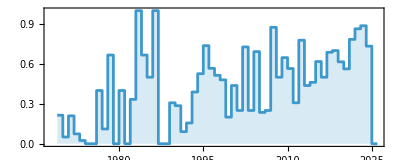

```mathematica
ListStepPlot[Quiet[Table[{i,Count[
$LifeData/@Keys[Select[resall,ContainsAny[#,{None}]&]],x_/;x["Year"]==i]/Count[$LifeData,x_/;x["Year"]==i]},{i,1969,2025}]/. Indeterminate->0],Filling->Axis,Frame->True,AspectRatio->.4]
```

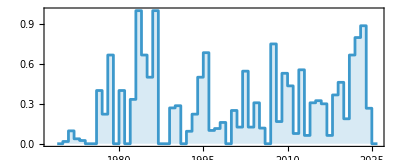

```mathematica
ListStepPlot[Quiet[Table[{i,Count[
$LifeData/@Keys[Select[oresall,ContainsAny[#,{None}]&]],x_/;x["Year"]==i]/Count[$LifeData,x_/;x["Year"]==i]},{i,1969,2025}]/. Indeterminate->0],Filling->Axis,Frame->True,AspectRatio->.4]
```

```mathematica
Quiet[Table[{i,{Count[
$LifeData/@Keys[Select[resall,ContainsAny[#,{None}]&]],x_/;x["Year"]==i],Count[$LifeData,x_/;x["Year"]==i]}},{i,1969,2025}]/. Indeterminate->0]
```

{{1969,{3,14}},{1970,{3,59}},{1971,{13,62}},{1972,{4,54}},{1973,{3,124}},{1974,{0,0}},{1975,{0,1}},{1976,{2,5}},{1977,{1,9}},{1978,{2,3}},{1979,{0,1}},{1980,{2,5}},{1981,{0,0}},{1982,{1,3}},{1983,{4,4}},{1984,{6,9}},{1985,{1,2}},{1986,{1,1}},{1987,{0,0}},{1988,{0,3}},{1989,{8,26}},{1990,{2,7}},{1991,{1,11}},{1992,{5,32}},{1993,{7,18}},{1994,{20,38}},{1995,{14,19}},{1996,{17,30}},{1997,{18,35}},{1998,{12,25}},{1999,{1,5}},{2000,{7,16}},{2001,{2,8}},{2002,{8,11}},{2003,{2,8}},{2004,{9,13}},{2005,{4,17}},{2006,{3,12}},{2007,{7,8}},{2008,{3,6}},{2009,{11,17}},{2010,{13,23}},{2011,{4,13}},{2012,{7,9}},{2013,{7,16}},{2014,{6,13}},{2015,{21,34}},{2016,{15,30}},{2017,{11,16}},{2018,{21,30}},{2019,{8,13}},{2020,{9,16}},{2021,{40,51}},{2022,{171,198}},{2023,{172,194}},{2024,{11,15}},{2025,{0,1}}}

### Loading v2

```mathematica
CanonicalParts[array_]:=PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@CausalSeparation[Position[array,1]]
```

```mathematica
PatternCheck[patt_,db_]:=If[#=!={},#[[1,1,1]],None]&[Position[db,patt]]
```

```mathematica
IsPrimitive[array_]:=Length[CausalSeparation[Position[array,1]]]==1
```

```mathematica
primitives=Select[Keys[Select[Select[$LifeData,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],IsPrimitive[Normal[$LifeData[#]["MatrixData"]]]&];
```

```mathematica
allprims=Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{PatternCanonicalize2[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[$LifeData[#]])&,primitives]];
```

```mathematica
xresall=Association[ParallelMap[#->MemoryConstrained[(PatternCheck[#,allprims]&/@Union[CanonicalParts[Normal[$LifeData[#]["MatrixData"]]]]),10^7]&,Keys[Select[Select[$LifeData,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]]/.(x_->{x_}):>(x->{None})];
```

### Running

#### res

But let’s say we’re just thinking about “primitive modular parts”.  There’s still the question of whether a new pattern involves only known such primitive parts---or whether it has de novo elements that have never been seen before. If we look at patterns where we can identify at least some pre-existing modular parts, we can ask what fraction of the time there are also de novo parts.  If we plot this by year, something we see is that there’s been a progressive trend since about 1990 towards more patterns having at least some de novo elements:

“If we look at patterns where we can identify at least some pre - existing modular parts” this isn’t what we’re doing though... we’re just looking at any old pattern

```mathematica
ListStepPlot[Quiet[Table[{i,Count[$LifeData/@Keys[Select[resall,ContainsAny[#,{None}]&]],x_/;x["Year"]==i]/Count[$LifeData,x_/;x["Year"]==i]},{i,1969,2025}]/. Indeterminate->0],Filling->Axis,Frame->True,AspectRatio->.4]
```

-Graphics-

I think this is what you’re describing:

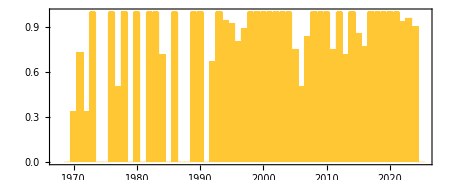

```mathematica
BarChart[Quiet[Table[Count[$LifeData/@Keys[Select[resall,MemberQ[#, None]&&Count[#, _String]>=1&]],x_/;x["Year"]==i]/Count[$LifeData/@Keys[Select[resall, Count[#, _String]>=1&]],x_/;x["Year"]==i],{i,1969,2025}]/. Indeterminate->0],Frame->True,AspectRatio->.4, FrameTicks->{{True, Automatic}, {Table[If[Mod[i , 10] == 2, {i,i + 1968}, i], {i, 2, 2025 - 1969 + 1, 10}], True}}]
```

```mathematica
Labeled[ArrayPlot[#MatrixData, ImageSize->{100, 100}], Text[#Name<>", "<>ToString[#Year]<>", "<>ToString[resall[#Name]]]]&/@Cases[$LifeData/@Keys[Select[resall,MemberQ[#, None]&&Count[#, _String]>=1&]],x_/;x["Year"]==1970]
```

{-Graphics-Gosper glider gun, 1970, {Block, None, None},-Graphics-Period-60 glider gun, 1970, {Block, None, Glider, None, None, None, None, None}}

```mathematica
Labeled[ArrayPlot[#MatrixData, ImageSize->{100, 100}], Text[#Name<>", "<>ToString[#Year]<>", "<>ToString[resall[#Name]]]]&/@Cases[$LifeData/@Keys[Select[resall, Count[#, _String]>=1&]],x_/;x["Year"]==1970]
```

{-Graphics-Blockade, 1970, {Block},-Graphics-Gosper glider gun, 1970, {Block, None, None},-Graphics-Honey farm, 1970, {Beehive},-Graphics-Period-60 glider gun, 1970, {Block, None, Glider, None, None, None, None, None},-Graphics-Queen bee shuttle, 1970, {Block, Queen bee},-Graphics-Tail, 1970, {Leg}}

#### Highlighting used

```mathematica
highlightdependents[patdata_, subpatsdata_]:= 
 ArrayPlot[ReplacePart[patdata["MatrixData"], 
Thread[#->Red]]]&[
intersectingidxs[patdata["MatrixData"], #MatrixData]&[
PatternCanonicalize2[Normal[#["MatrixData"]]]&/@ subpatsdata
]]
```

```mathematica
Position[resall, "Gosper glider gun"]
```

{}

```mathematica
KeyValueMap[highlightdependents[$LifeData[#1], DeleteCases[#2, None]]&, ]
```

```mathematica
hihglightresall["Gosper glider gun"]
```

{Block,None,None}

```mathematica
highlightdependents[]
```

#### zooming in on 1969 for example

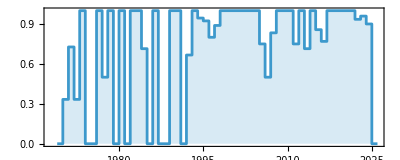

```mathematica
ListStepPlot[Quiet[Table[{i,Count[$LifeData/@Keys[Select[resall,MemberQ[#, None]&&Count[#, _String]>=1&]],x_/;x["Year"]==i]/Count[$LifeData/@Keys[Select[resall, Count[#, _String]>=1&]],x_/;x["Year"]==i]},{i,1969,2025}]/. Indeterminate->0],Filling->Axis,Frame->True,AspectRatio->.4]
```

#### xres

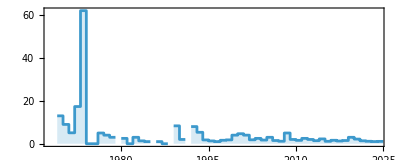

```mathematica
ListStepPlot[Quiet[Table[{i,Count[$LifeData/@Keys[Select[xresall,MemberQ[#, None]&]],x_/;x["Year"]==i]/Count[$LifeData/@Keys[Select[xresall, Count[#, _String]>=1&]],x_/;x["Year"]==i]},{i,1969,2025}]/. Indeterminate->0],Filling->Axis,Frame->True,AspectRatio->.4, PlotRange->All]
```

#### xres v2

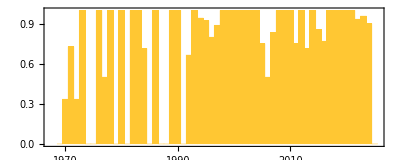

```mathematica
BarChart[Quiet[Table[Count[$LifeData/@Keys[Select[xresall,MemberQ[#, None]&&Count[#, _String]>=1&]],x_/;x["Year"]==i]/Count[$LifeData/@Keys[Select[xresall, Count[#, _String]>=1&]],x_/;x["Year"]==i],{i,1969,2025}]/. Indeterminate->0],Frame->True,AspectRatio->.4, FrameTicks->{{True, Automatic}, {Table[If[Mod[i , 10] == 2, {i,i + 1968}, i], {i, 2, 2025 - 1969 + 1, 10}], True}}]
```

#### v3

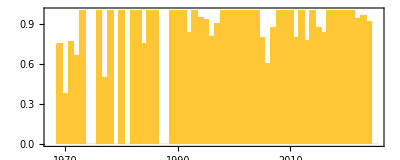

```mathematica
BarChart[Quiet[Table[Count[$LifeData/@Keys[Select[resall,ContainsAny[#,{None}]&]],x_/;x["Year"]==i]/Count[$LifeData/@Keys[resall],x_/;x["Year"]==i],{i,1969,2025}]/. Indeterminate->0],Frame->True,AspectRatio->.4, FrameTicks->{{True, Automatic}, {Table[If[Mod[i , 10] == 2, {i,i + 1968}, i], {i, 2, 2025 - 1969 + 1, 10}], True}}]
```

#### v4

```mathematica
Accumulate Count[$LifeData/@Keys[Select[resall, Count[#, _String]>=1&]],x_/;x["Year"]==i]
```

0

Average by year of ratio of nones to normal?

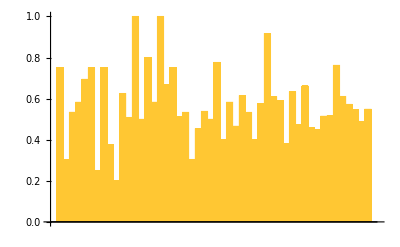

```mathematica
BarChart[Values[Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]/ Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]]
```

```mathematica
BarChart[Values[Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]/ Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]]
```

```mathematica
BarChart[{Values[Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]],   ]
```

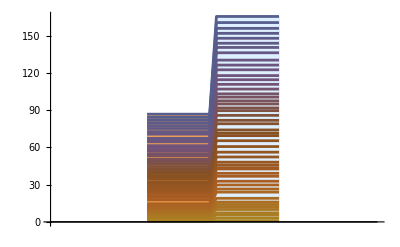

```mathematica
BarChart[{Style[Values[Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]], Lighter[Orange]] ,
Style[Values[Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Length/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]], LightBlue]}, ChartLayout->"Stacked", Joined->True]
```

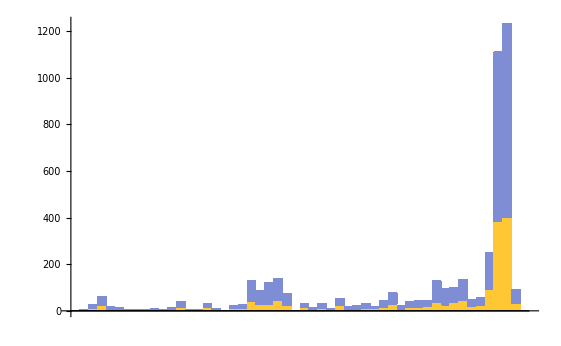

Lookup::invrl: The argument #1 is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

{Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0],Lookup[#1,i,0]}

```mathematica
BarChart[Transpose@{(*Style[*)Values[Total[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]] ,
Values[Total[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Length/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]}, ChartLayout->"Stacked"]
```

```mathematica
(Table[Lookup[#, i, 0], {i, 1969, 2025}]&/@{(*Style[*)Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&] ,
Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Length/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]})
```

{{3/4,9/8,23/17,1,5/3,0,0,3/2,1/2,3/2,0,1,0,1,3/2,7/4,3,2,0,0,13/8,2,1,4/3,10/7,41/21,28/15,4/3,43/20,2,1,13/7,2,11/8,2,7/3,6/5,1,3/2,8/3,14/11,29/13,6/5,13/7,14/9,3,37/24,25/18,36/11,44/21,5/2,7/3,9/4,384/181,400/179,31/12,0},{1,17/8,40/17,11/6,8/3,0,0,2,2,2,0,3,0,5,5/2,13/4,3,4,0,0,19/8,7/2,1,13/6,16/7,88/21,58/15,95/21,47/10,49/12,2,18/7,5,11/4,4,34/9,11/5,16/5,5/2,3,29/11,50/13,19/5,26/7,10/3,14/3,91/24,4,65/11,30/7,27/8,4,159/40,726/181,834/179,59/12,0}}

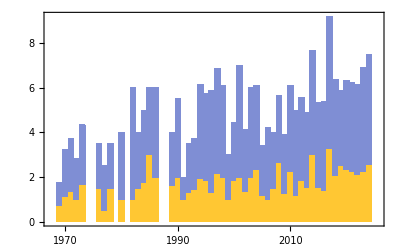

```mathematica
BarChart[Transpose@
(Table[Lookup[#, i, 0], {i, 1969, 2025}]&/@{(*Style[*)Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&] ,
Mean[#[[All, 2]]]&/@GroupBy[Normal[Quiet[(Length/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]}), ChartLayout->"Stacked",FrameTicks->{{True, Automatic}, {Table[If[Mod[i , 10] == 2, {i,i + 1968}, i], {i, 2, 2025 - 1969 + 1, 10}], True}}, Frame->True ]
```

```mathematica
RandomReal[1,{4,5}]
```

{{0.580474,0.128821,0.306427,0.712012,0.390582},{0.819967,0.325351,0.59326,0.518774,0.169013},{0.472565,0.807161,0.0118355,0.316876,0.789804},{0.011978,0.391276,0.458902,0.458845,0.727517}}

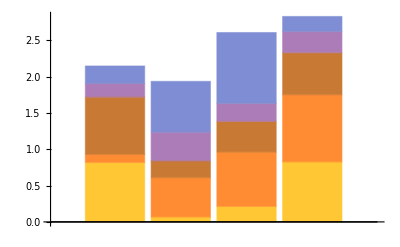
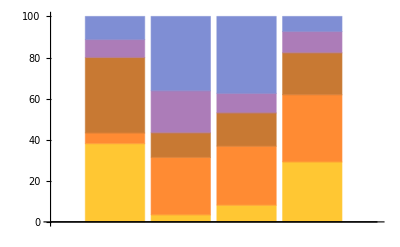

```mathematica
Table[BarChart[SeedRandom[1];RandomReal[1,{4,5}],ChartLayout->l],{l,{"Stacked","Percentile"}}]
```

```mathematica
/ Length[#]
```

```mathematica
GroupBy[Normal[Quiet[(Count[#, None]/ Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&][[All, All, 2]]
```

<|1969→{1,1,1,0},1970→{0,1,2/3,0,3/4,0,0,0},1971→{1,2/3,1/4,1,3/5,0,1,2/5,0,1,0,2/3,1/2,1,0,1/2,1/2},1972→{0,0,1/2,1,1,1},1973→{3/4,1/3,1},1976→{1,1/2},1977→{1/2,0},1978→{1,1/2},1980→{1/2,1/4},1982→{1/5},1983→{1/2,1/2,1/2,1},1984→{1/2,1/2,4/5,0,0,2/3,3/5,1},1985→{1},1986→{1/2},1989→{2/5,1,1/3,1,1,1,2/3,1},1990→{1/2,2/3},1991→{1},1992→{1,1/2,1,0,1/2,1},1993→{1,1,1,1/4,1/2,1,1/2},1994→{1/3,1/2,1/2,0,1/3,1,1,1/4,1,4/5,3/5,1/2,3/7,3/7,2/5,3/7,1/2,1/3,2/5,1/2,1/2},1995→{1/3,2/3,1/2,1/4,1,1/2,3/4,3/5,2/3,0,4/7,1/2,1/2,1/6,1},1996→{1/2,3/7,0,1/5,1/4,0,1/2,1/5,0,0,1/7,1/5,1/6,1/5,1/2,1/3,1/2,3/7,1/3,1,1/2},1997→{1,0,1/2,2/5,2/5,1/5,1/3,1/4,0,5/9,2/5,1,5/7,1/4,5/8,1/3,1/3,3/7,2/3,2/3},1998→{2/5,3/7,1/3,1,3/5,1/2,1/5,1/2,1/4,1,3/4,1/2},1999→{1/2},2000→{1,1,1,1,1/3,3/5,1/2},2001→{1/5,3/5},2002→{1/3,1/3,1,1/2,1,1/2,1/3,2/3},2003→{1/3,3/5},2004→{1,7/9,1/4,1/3,1/3,1/2,2/3,2/3,1},2005→{1/2,1,1/2,2/3,0},2006→{1,0,1/3,0,2/3},2007→{1,1/3,0,1/2,1/2,1,3/5,2/3},2008→{1,1,3/4},2009→{1/2,1/3,1,1,1/2,1/3,1/2,1,1,1/3,1/5},2010→{3/4,1/2,1/3,1,1/2,3/4,1/2,1/2,2/3,3/5,5/8,3/5,1/3},2011→{1/5,0,1,1/2,1/5},2012→{1,1/3,1/2,2/5,1,1/5,1},2013→{1/3,0,1/2,0,1,5/6,1/3,1/4,1},2014→{2/3,1,1/3,1,10/13,1/5},2015→{2/7,2/3,1/2,0,0,2/3,1/3,1/3,1/4,1/4,1/5,1/2,2/3,1,0,1/2,1/2,1/4,1/3,1/2,1,3/4,1,1/2},2016→{1,1/3,1,1/5,1,2/3,1/6,1/4,1/3,0,1/4,0,1/6,0,1/2,1,1/5,1},2017→{7/8,8/9,1/3,1/3,2/5,1/3,3/5,4/7,3/5,2/5,1/3},2018→{1/2,1/2,1/3,1,1/3,1,1/2,1/2,2/3,1/5,3/8,2/5,1/2,1/3,1/3,4/5,1,1/4,5/7,2/7,1/3},2019→{1,1,1,1/4,3/5,1,3/4,1/2},2020→{1/2,1,1,1/5,1/2,2/3,3/7,1/5,1},2021→{2/3,1/2,1/4,1/2,1/5,1,1/3,1/2,1/5,1,1/4,1/3,4/5,1/4,2/3,1/3,2/3,1/2,3/5,1/2,1,1/2,2/3,1/2,1,1/3,3/4,4/5,2/3,1/3,1/5,3/4,4/5,1/5,1,1/2,1/3,1,1/2,1},2022→{4/5,1/4,1/2,1,1,1,1/3,1/2,1,2/3,1/2,2/3,1/5,1/4,1/4,1/2,1/2,1,1/3,1/3,0,2/3,1/4,0,1/3,1/2,1/2,1/3,1/3,2/3,1/2,1/3,1/2,1/3,2/3,1,2/5,1/3,0,1/5,5/6,2/3,1/2,1/3,0,1/4,1,4/7,0,1/2,2/3,3/4,2/3,1/2,2/3,1/4,2/5,1/2,0,1/3,2/5,1/3,1/3,2/3,1/2,7/11,2/3,5/7,2/5,3/5,2/3,2/3,1,2/3,1,1,1,1/2,4/5,2/3,1/2,2/3,1/3,3/4,1/2,1/2,1/4,3/4,1/5,3/5,1/3,1/2,2/3,2/3,1/3,1/3,2/3,1,1,2/3,1/2,1/4,3/5,1/3,3/5,1/4,1,1/5,1/2,1,2/3,2/3,1/2,5/6,4/5,2/3,1/3,1/5,1/2,2/3,1,3/4,1,1,4/7,1/2,1,3/7,1/2,1/4,1/4,1/2,0,2/7,2/5,5/8,1/4,2/5,5/7,3/5,1/2,1/2,1/3,3/5,1/2,1/2,2/5,0,3/5,2/7,0,3/7,1,0,2/3,1,2/3,1,2/3,1/2,1,1/2,2/3,1/2,1/3,2/3,1,1/2,2/5,3/8,1,1,1,3/4,3/4,2/3,2/5,2/3,3/5,1/5,1/3},2023→{1/2,1/2,1/2,1/2,0,1/3,1/2,1/3,1/3,2/3,2/3,1/2,2/3,1/3,1/2,1/2,1/2,1/4,1/3,2/3,3/5,3/5,1/4,1/7,3/5,1,2/5,1/3,2/3,1/3,1/3,2/3,1/2,1/3,2/3,7/10,1/3,1,1,1/4,3/4,1/2,1/2,3/5,1,3/4,2/5,1,1,4/7,1/4,1/4,1/2,3/5,2/5,2/3,1/2,1/2,2/3,3/4,1/5,2/5,1/2,2/5,1/3,1/4,1/4,1/2,3/4,1/3,1/2,2/3,1/2,1/3,3/4,1,1/2,1/2,3/5,2/3,7/8,1/5,2/3,1/5,1/2,1/2,3/4,0,3/5,3/5,2/3,0,0,3/5,1/3,4/7,0,1/3,2/3,2/5,1/5,4/7,4/7,3/5,1/4,1/4,1/5,2/5,1/5,5/7,1/2,1/2,1/2,1/4,1/4,2/5,1/4,1/3,2/5,1/4,1/5,4/9,1/2,1/3,2/3,1/2,2/5,2/5,0,2/7,2/5,2/5,1,1/3,2/3,4/7,2/3,1/2,2/3,1/2,1/7,1/2,1/3,5/8,3/5,3/4,3/7,3/5,3/4,3/5,1/2,3/8,4/5,2/3,1/4,1/2,1/4,4/5,2/7,3/4,1/4,1/2,2/3,4/7,3/7,1/2,1/4,2/3,2/3,0,3/5,2/3,2/3,3/8,1/2,7/13,3/4,2/3,1/3},2024→{1/3,1,1,1/3,3/4,0,1/5,5/8,1/2,4/7,7/9,1/2}|>

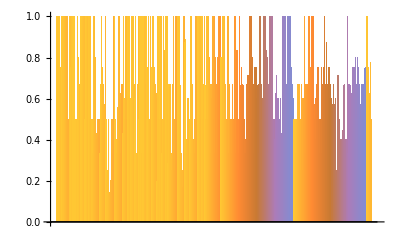

```mathematica
BarChart[GroupBy[Normal[Quiet[(Count[#, None]/ Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&][[All, All, 2]]]
```

```mathematica
Table[i, {i, 1969, 2025}]
```

```mathematica
Table[Count[$LifeData/@Quiet[(Count[#, None]/ Length[#]&/@resall)/.Indeterminate->0],x_/;x["Year"]==i],{i,1969,2025}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

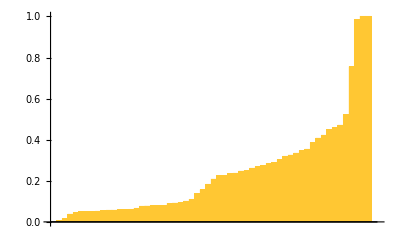

```mathematica
BarChart[Accumulate[#]/ Total[#]&@Table[Count[$LifeData/@Keys[resall],x_/;x["Year"]==i],{i,1969,2025}]]
```

```mathematica
Table[Count[$LifeData/@Keys[resall],x_/;x["Year"]==i],{i,1969,2025}]
```

{4,8,17,6,3,0,0,2,2,2,0,2,0,1,4,8,1,1,0,0,8,2,1,6,7,21,15,21,20,12,1,7,2,8,2,9,5,5,8,3,11,13,5,7,9,6,24,18,11,21,8,9,40,181,179,12,0}

#### 3D version

```mathematica
ListPointPlot3D[{Catenate[KeyValueMap[Function[{year, items}, MapIndexed[{year, #2[[1]], #[[2]]}&, items]], GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]],
Catenate[KeyValueMap[Function[{year, items}, MapIndexed[{year,#2[[1]], #[[2]]}&, items]], GroupBy[Normal[Quiet[(Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]]}
, Filling->Bottom]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{{{1, 1, 1}}, {{2, 2, 2}}}]
```

-Graphics3D-

```mathematica
ListPlot3D[{Catenate[KeyValueMap[Function[{year, items}, MapIndexed[{year, #2[[1]], #[[2]]}&, items]], GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]],
Catenate[KeyValueMap[Function[{year, items}, MapIndexed[{year,#2[[1]], #[[2]]}&, items]], GroupBy[Normal[Quiet[(Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]]}
, Filling->Bottom]
```

-Graphics3D-

```mathematica
Histogram3D[{Catenate[KeyValueMap[Function[{year, items}, MapIndexed[{year, #2[[1]], #[[2]]}&, items]], GroupBy[Normal[Quiet[(Count[#, None]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]],
Catenate[KeyValueMap[Function[{year, items}, MapIndexed[{year,#2[[1]], #[[2]]}&, items]], GroupBy[Normal[Quiet[(Length[#]&/@resall)/.Indeterminate->0]], $LifeData[#[[1]]]["Year"]&]]]}
]
```

Histogram3D::ldata: {{{1969,1,1},{1969,2,1},{1969,3,1},{1969,4,0},{1970,1,0},{1970,2,1},{1970,3,2},{1970,4,0},{1970,5,6},{1970,6,0},{1970,7,0},{1970,8,0},{1971,1,4},{1971,2,2},«23»,{1973,3,1},{1976,1,2},{1976,2,1},{1977,1,1},{1977,2,0},{1978,1,2},{1978,2,1},{1980,1,1},{1980,2,1},{1982,1,1},{1983,1,1},{1983,2,2},{1983,3,1},«728»},{«1»}} is not a valid dataset or list of datasets.

Histogram3D[{{{1969,1,1},{1969,2,1},{1969,3,1},{1969,4,0},{1970,1,0},{1970,2,1},{1970,3,2},{1970,4,0},{1970,5,6},{1970,6,0},{1970,7,0},{1970,8,0},{1971,1,4},{1971,2,2},{1971,3,1},{1971,4,2},{1971,5,3},{1971,6,0},{1971,7,1},{1971,8,2},{1971,9,0},{1971,10,1},{1971,11,0},{1971,12,2},{1971,13,1},{1971,14,2},{1971,15,0},{1971,16,1},{1971,17,1},{1972,1,0},{1972,2,0},{1972,3,1},{1972,4,2},{1972,5,1},{1972,6,2},{1973,1,3},{1973,2,1},{1973,3,1},{1976,1,2},{1976,2,1},{1977,1,1},{1977,2,0},{1978,1,2},{1978,2,1},{1980,1,1},{1980,2,1},{1982,1,1},{1983,1,1},{1983,2,2},{1983,3,1},{1983,4,2},{1984,1,2},{1984,2,1},{1984,3,4},{1984,4,0},{1984,5,0},{1984,6,2},{1984,7,3},{1984,8,2},{1985,1,3},{1986,1,2},{1989,1,2},{1989,2,2},{1989,3,1},{1989,4,1},{1989,5,2},{1989,6,1},{1989,7,2},{1989,8,2},{1990,1,2},{1990,2,2},{1991,1,1},{1992,1,1},{1992,2,1},{1992,3,3},{1992,4,0},{1992,5,1},{1992,6,2},{1993,1,1},{1993,2,1},{1993,3,2},{1993,4,1},{1993,5,2},{1993,6,2},{1993,7,1},{1994,1,1},{1994,2,3},{1994,3,1},{1994,4,0},{1994,5,1},{1994,6,1},{1994,7,1},{1994,8,1},{1994,9,2},{1994,10,4},{1994,11,3},{1994,12,4},{1994,13,3},{1994,14,3},{1994,15,2},{1994,16,3},{1994,17,1},{1994,18,2},{1994,19,2},{1994,20,1},{1994,21,2},{1995,1,1},{1995,2,2},{1995,3,1},{1995,4,1},{1995,5,2},{1995,6,3},{1995,7,3},{1995,8,3},{1995,9,2},{1995,10,0},{1995,11,4},{1995,12,2},{1995,13,1},{1995,14,1},{1995,15,2},{1996,1,1},{1996,2,3},{1996,3,0},{1996,4,1},{1996,5,1},{1996,6,0},{1996,7,2},{1996,8,1},{1996,9,0},{1996,10,0},{1996,11,1},{1996,12,1},{1996,13,1},{1996,14,1},{1996,15,1},{1996,16,2},{1996,17,3},{1996,18,3},{1996,19,1},{1996,20,2},{1996,21,3},{1997,1,2},{1997,2,0},{1997,3,1},{1997,4,2},{1997,5,2},{1997,6,1},{1997,7,2},{1997,8,1},{1997,9,0},{1997,10,5},{1997,11,2},{1997,12,3},{1997,13,5},{1997,14,1},{1997,15,5},{1997,16,1},{1997,17,1},{1997,18,3},{1997,19,4},{1997,20,2},{1998,1,2},{1998,2,3},{1998,3,2},{1998,4,3},{1998,5,3},{1998,6,2},{1998,7,1},{1998,8,1},{1998,9,1},{1998,10,2},{1998,11,3},{1998,12,1},{1999,1,1},{2000,1,3},{2000,2,2},{2000,3,2},{2000,4,1},{2000,5,1},{2000,6,3},{2000,7,1},{2001,1,1},{2001,2,3},{2002,1,1},{2002,2,1},{2002,3,2},{2002,4,1},{2002,5,1},{2002,6,1},{2002,7,2},{2002,8,2},{2003,1,1},{2003,2,3},{2004,1,2},{2004,2,7},{2004,3,1},{2004,4,1},{2004,5,1},{2004,6,1},{2004,7,2},{2004,8,4},{2004,9,2},{2005,1,1},{2005,2,2},{2005,3,1},{2005,4,2},{2005,5,0},{2006,1,2},{2006,2,0},{2006,3,1},{2006,4,0},{2006,5,2},{2007,1,3},{2007,2,1},{2007,3,0},{2007,4,1},{2007,5,1},{2007,6,1},{2007,7,3},{2007,8,2},{2008,1,3},{2008,2,2},{2008,3,3},{2009,1,1},{2009,2,1},{2009,3,1},{2009,4,1},{2009,5,1},{2009,6,1},{2009,7,1},{2009,8,2},{2009,9,2},{2009,10,2},{2009,11,1},{2010,1,3},{2010,2,1},{2010,3,1},{2010,4,2},{2010,5,2},{2010,6,3},{2010,7,1},{2010,8,1},{2010,9,2},{2010,10,3},{2010,11,5},{2010,12,3},{2010,13,2},{2011,1,1},{2011,2,0},{2011,3,2},{2011,4,2},{2011,5,1},{2012,1,2},{2012,2,2},{2012,3,2},{2012,4,2},{2012,5,1},{2012,6,1},{2012,7,3},{2013,1,1},{2013,2,0},{2013,3,2},{2013,4,0},{2013,5,2},{2013,6,5},{2013,7,1},{2013,8,1},{2013,9,2},{2014,1,2},{2014,2,2},{2014,3,1},{2014,4,2},{2014,5,10},{2014,6,1},{2015,1,2},{2015,2,2},{2015,3,2},{2015,4,0},{2015,5,0},{2015,6,2},{2015,7,1},{2015,8,1},{2015,9,1},{2015,10,2},{2015,11,1},{2015,12,1},{2015,13,2},{2015,14,2},{2015,15,0},{2015,16,2},{2015,17,2},{2015,18,1},{2015,19,2},{2015,20,1},{2015,21,2},{2015,22,3},{2015,23,3},{2015,24,2},{2016,1,2},{2016,2,1},{2016,3,4},{2016,4,1},{2016,5,2},{2016,6,2},{2016,7,1},{2016,8,1},{2016,9,2},{2016,10,0},{2016,11,1},{2016,12,0},{2016,13,1},{2016,14,0},{2016,15,1},{2016,16,2},{2016,17,1},{2016,18,3},{2017,1,7},{2017,2,8},{2017,3,2},{2017,4,2},{2017,5,2},{2017,6,2},{2017,7,3},{2017,8,4},{2017,9,3},{2017,10,2},{2017,11,1},{2018,1,1},{2018,2,1},{2018,3,1},{2018,4,1},{2018,5,2},{2018,6,3},{2018,7,3},{2018,8,1},{2018,9,2},{2018,10,1},{2018,11,3},{2018,12,2},{2018,13,1},{2018,14,1},{2018,15,2},{2018,16,8},{2018,17,2},{2018,18,1},{2018,19,5},{2018,20,2},{2018,21,1},{2019,1,2},{2019,2,2},{2019,3,6},{2019,4,1},{2019,5,3},{2019,6,2},{2019,7,3},{2019,8,1},{2020,1,1},{2020,2,5},{2020,3,5},{2020,4,1},{2020,5,1},{2020,6,2},{2020,7,3},{2020,8,1},{2020,9,2},{2021,1,2},{2021,2,1},{2021,3,1},{2021,4,2},{2021,5,1},{2021,6,4},{2021,7,1},{2021,8,2},{2021,9,1},{2021,10,2},{2021,11,1},{2021,12,2},{2021,13,4},{2021,14,1},{2021,15,2},{2021,16,1},{2021,17,4},{2021,18,3},{2021,19,3},{2021,20,1},{2021,21,2},{2021,22,1},{2021,23,2},{2021,24,2},{2021,25,6},{2021,26,1},{2021,27,3},{2021,28,4},{2021,29,2},{2021,30,1},{2021,31,1},{2021,32,3},{2021,33,4},{2021,34,1},{2021,35,6},{2021,36,3},{2021,37,1},{2021,38,3},{2021,39,2},{2021,40,3},{2022,1,4},{2022,2,1},{2022,3,2},{2022,4,3},{2022,5,10},{2022,6,1},{2022,7,1},{2022,8,1},{2022,9,2},{2022,10,2},{2022,11,2},{2022,12,2},{2022,13,1},{2022,14,1},{2022,15,1},{2022,16,2},{2022,17,1},{2022,18,2},{2022,19,1},{2022,20,2},{2022,21,0},{2022,22,2},{2022,23,1},{2022,24,0},{2022,25,1},{2022,26,1},{2022,27,2},{2022,28,1},{2022,29,1},{2022,30,2},{2022,31,1},{2022,32,1},{2022,33,2},{2022,34,1},{2022,35,2},{2022,36,3},{2022,37,2},{2022,38,1},{2022,39,0},{2022,40,1},{2022,41,5},{2022,42,2},{2022,43,1},{2022,44,2},{2022,45,0},{2022,46,1},{2022,47,2},{2022,48,4},{2022,49,0},{2022,50,2},{2022,51,2},{2022,52,3},{2022,53,2},{2022,54,2},{2022,55,2},{2022,56,1},{2022,57,2},{2022,58,1},{2022,59,0},{2022,60,1},{2022,61,2},{2022,62,1},{2022,63,1},{2022,64,2},{2022,65,3},{2022,66,7},{2022,67,2},{2022,68,5},{2022,69,2},{2022,70,3},{2022,71,2},{2022,72,6},{2022,73,2},{2022,74,2},{2022,75,1},{2022,76,1},{2022,77,2},{2022,78,1},{2022,79,4},{2022,80,2},{2022,81,1},{2022,82,2},{2022,83,1},{2022,84,3},{2022,85,1},{2022,86,2},{2022,87,1},{2022,88,3},{2022,89,1},{2022,90,3},{2022,91,1},{2022,92,2},{2022,93,2},{2022,94,2},{2022,95,1},{2022,96,1},{2022,97,4},{2022,98,2},{2022,99,6},{2022,100,4},{2022,101,1},{2022,102,1},{2022,103,3},{2022,104,1},{2022,105,3},{2022,106,1},{2022,107,3},{2022,108,1},{2022,109,2},{2022,110,3},{2022,111,6},{2022,112,2},{2022,113,2},{2022,114,5},{2022,115,4},{2022,116,2},{2022,117,1},{2022,118,1},{2022,119,1},{2022,120,2},{2022,121,3},{2022,122,3},{2022,123,4},{2022,124,3},{2022,125,4},{2022,126,3},{2022,127,6},{2022,128,3},{2022,129,1},{2022,130,1},{2022,131,1},{2022,132,2},{2022,133,0},{2022,134,2},{2022,135,2},{2022,136,5},{2022,137,1},{2022,138,2},{2022,139,5},{2022,140,3},{2022,141,3},{2022,142,1},{2022,143,2},{2022,144,3},{2022,145,2},{2022,146,1},{2022,147,2},{2022,148,0},{2022,149,3},{2022,150,2},{2022,151,0},{2022,152,3},{2022,153,2},{2022,154,0},{2022,155,2},{2022,156,3},{2022,157,2},{2022,158,2},{2022,159,2},{2022,160,1},{2022,161,5},{2022,162,2},{2022,163,4},{2022,164,2},{2022,165,2},{2022,166,2},{2022,167,5},{2022,168,2},{2022,169,2},{2022,170,3},{2022,171,2},{2022,172,2},{2022,173,3},{2022,174,3},{2022,175,3},{2022,176,2},{2022,177,2},{2022,178,2},{2022,179,3},{2022,180,1},{2022,181,1},{2023,1,3},{2023,2,2},{2023,3,2},{2023,4,2},{2023,5,0},{2023,6,1},{2023,7,2},{2023,8,1},{2023,9,1},{2023,10,2},{2023,11,2},{2023,12,1},{2023,13,2},{2023,14,1},{2023,15,1},{2023,16,2},{2023,17,1},{2023,18,1},{2023,19,1},{2023,20,2},{2023,21,3},{2023,22,3},{2023,23,1},{2023,24,1},{2023,25,3},{2023,26,3},{2023,27,2},{2023,28,1},{2023,29,2},{2023,30,1},{2023,31,1},{2023,32,2},{2023,33,2},{2023,34,1},{2023,35,6},{2023,36,7},{2023,37,2},{2023,38,2},{2023,39,2},{2023,40,1},{2023,41,3},{2023,42,2},{2023,43,1},{2023,44,3},{2023,45,3},{2023,46,3},{2023,47,2},{2023,48,2},{2023,49,2},{2023,50,4},{2023,51,1},{2023,52,1},{2023,53,2},{2023,54,3},{2023,55,2},{2023,56,2},{2023,57,2},{2023,58,2},{2023,59,2},{2023,60,3},{2023,61,1},{2023,62,2},{2023,63,2},{2023,64,2},{2023,65,2},{2023,66,1},{2023,67,1},{2023,68,3},{2023,69,3},{2023,70,1},{2023,71,2},{2023,72,6},{2023,73,4},{2023,74,1},{2023,75,6},{2023,76,4},{2023,77,2},{2023,78,1},{2023,79,3},{2023,80,2},{2023,81,7},{2023,82,1},{2023,83,2},{2023,84,1},{2023,85,2},{2023,86,1},{2023,87,3},{2023,88,0},{2023,89,3},{2023,90,3},{2023,91,2},{2023,92,0},{2023,93,0},{2023,94,3},{2023,95,1},{2023,96,4},{2023,97,0},{2023,98,2},{2023,99,2},{2023,100,2},{2023,101,1},{2023,102,4},{2023,103,4},{2023,104,3},{2023,105,1},{2023,106,2},{2023,107,1},{2023,108,2},{2023,109,1},{2023,110,5},{2023,111,3},{2023,112,3},{2023,113,2},{2023,114,1},{2023,115,1},{2023,116,2},{2023,117,1},{2023,118,2},{2023,119,2},{2023,120,1},{2023,121,1},{2023,122,4},{2023,123,2},{2023,124,2},{2023,125,4},{2023,126,2},{2023,127,2},{2023,128,2},{2023,129,0},{2023,130,2},{2023,131,2},{2023,132,2},{2023,133,3},{2023,134,1},{2023,135,4},{2023,136,4},{2023,137,2},{2023,138,3},{2023,139,2},{2023,140,2},{2023,141,1},{2023,142,2},{2023,143,2},{2023,144,5},{2023,145,3},{2023,146,3},{2023,147,3},{2023,148,3},{2023,149,3},{2023,150,3},{2023,151,2},{2023,152,3},{2023,153,4},{2023,154,2},{2023,155,1},{2023,156,2},{2023,157,1},{2023,158,4},{2023,159,2},{2023,160,3},{2023,161,1},{2023,162,2},{2023,163,2},{2023,164,4},{2023,165,3},{2023,166,2},{2023,167,1},{2023,168,2},{2023,169,2},{2023,170,0},{2023,171,3},{2023,172,4},{2023,173,2},{2023,174,3},{2023,175,4},{2023,176,7},{2023,177,3},{2023,178,4},{2023,179,2},{2024,1,1},{2024,2,2},{2024,3,2},{2024,4,2},{2024,5,3},{2024,6,0},{2024,7,1},{2024,8,5},{2024,9,2},{2024,10,4},{2024,11,7},{2024,12,2}},{{1969,1,1},{1969,2,1},{1969,3,1},{1969,4,1},{1970,1,1},{1970,2,1},{1970,3,3},{1970,4,1},{1970,5,8},{1970,6,0},{1970,7,2},{1970,8,1},{1971,1,4},{1971,2,3},{1971,3,4},{1971,4,2},{1971,5,5},{1971,6,0},{1971,7,1},{1971,8,5},{1971,9,1},{1971,10,1},{1971,11,2},{1971,12,3},{1971,13,2},{1971,14,2},{1971,15,1},{1971,16,2},{1971,17,2},{1972,1,1},{1972,2,3},{1972,3,2},{1972,4,2},{1972,5,1},{1972,6,2},{1973,1,4},{1973,2,3},{1973,3,1},{1976,1,2},{1976,2,2},{1977,1,2},{1977,2,2},{1978,1,2},{1978,2,2},{1980,1,2},{1980,2,4},{1982,1,5},{1983,1,2},{1983,2,4},{1983,3,2},{1983,4,2},{1984,1,4},{1984,2,2},{1984,3,5},{1984,4,3},{1984,5,2},{1984,6,3},{1984,7,5},{1984,8,2},{1985,1,3},{1986,1,4},{1989,1,5},{1989,2,2},{1989,3,3},{1989,4,1},{1989,5,2},{1989,6,1},{1989,7,3},{1989,8,2},{1990,1,4},{1990,2,3},{1991,1,1},{1992,1,1},{1992,2,2},{1992,3,3},{1992,4,3},{1992,5,2},{1992,6,2},{1993,1,1},{1993,2,1},{1993,3,2},{1993,4,4},{1993,5,4},{1993,6,2},{1993,7,2},{1994,1,3},{1994,2,6},{1994,3,2},{1994,4,3},{1994,5,3},{1994,6,1},{1994,7,1},{1994,8,4},{1994,9,2},{1994,10,5},{1994,11,5},{1994,12,8},{1994,13,7},{1994,14,7},{1994,15,5},{1994,16,7},{1994,17,2},{1994,18,6},{1994,19,5},{1994,20,2},{1994,21,4},{1995,1,3},{1995,2,3},{1995,3,2},{1995,4,4},{1995,5,2},{1995,6,6},{1995,7,4},{1995,8,5},{1995,9,3},{1995,10,5},{1995,11,7},{1995,12,4},{1995,13,2},{1995,14,6},{1995,15,2},{1996,1,2},{1996,2,7},{1996,3,2},{1996,4,5},{1996,5,4},{1996,6,3},{1996,7,4},{1996,8,5},{1996,9,4},{1996,10,4},{1996,11,7},{1996,12,5},{1996,13,6},{1996,14,5},{1996,15,2},{1996,16,6},{1996,17,6},{1996,18,7},{1996,19,3},{1996,20,2},{1996,21,6},{1997,1,2},{1997,2,4},{1997,3,2},{1997,4,5},{1997,5,5},{1997,6,5},{1997,7,6},{1997,8,4},{1997,9,3},{1997,10,9},{1997,11,5},{1997,12,3},{1997,13,7},{1997,14,4},{1997,15,8},{1997,16,3},{1997,17,3},{1997,18,7},{1997,19,6},{1997,20,3},{1998,1,5},{1998,2,7},{1998,3,6},{1998,4,3},{1998,5,5},{1998,6,4},{1998,7,5},{1998,8,2},{1998,9,4},{1998,10,2},{1998,11,4},{1998,12,2},{1999,1,2},{2000,1,3},{2000,2,2},{2000,3,2},{2000,4,1},{2000,5,3},{2000,6,5},{2000,7,2},{2001,1,5},{2001,2,5},{2002,1,3},{2002,2,3},{2002,3,2},{2002,4,2},{2002,5,1},{2002,6,2},{2002,7,6},{2002,8,3},{2003,1,3},{2003,2,5},{2004,1,2},{2004,2,9},{2004,3,4},{2004,4,3},{2004,5,3},{2004,6,2},{2004,7,3},{2004,8,6},{2004,9,2},{2005,1,2},{2005,2,2},{2005,3,2},{2005,4,3},{2005,5,2},{2006,1,2},{2006,2,3},{2006,3,3},{2006,4,5},{2006,5,3},{2007,1,3},{2007,2,3},{2007,3,1},{2007,4,2},{2007,5,2},{2007,6,1},{2007,7,5},{2007,8,3},{2008,1,3},{2008,2,2},{2008,3,4},{2009,1,2},{2009,2,3},{2009,3,1},{2009,4,1},{2009,5,2},{2009,6,3},{2009,7,2},{2009,8,2},{2009,9,2},{2009,10,6},{2009,11,5},{2010,1,4},{2010,2,2},{2010,3,3},{2010,4,2},{2010,5,4},{2010,6,4},{2010,7,2},{2010,8,2},{2010,9,3},{2010,10,5},{2010,11,8},{2010,12,5},{2010,13,6},{2011,1,5},{2011,2,3},{2011,3,2},{2011,4,4},{2011,5,5},{2012,1,2},{2012,2,6},{2012,3,4},{2012,4,5},{2012,5,1},{2012,6,5},{2012,7,3},{2013,1,3},{2013,2,2},{2013,3,4},{2013,4,4},{2013,5,2},{2013,6,6},{2013,7,3},{2013,8,4},{2013,9,2},{2014,1,3},{2014,2,2},{2014,3,3},{2014,4,2},{2014,5,13},{2014,6,5},{2015,1,7},{2015,2,3},{2015,3,4},{2015,4,5},{2015,5,3},{2015,6,3},{2015,7,3},{2015,8,3},{2015,9,4},{2015,10,8},{2015,11,5},{2015,12,2},{2015,13,3},{2015,14,2},{2015,15,3},{2015,16,4},{2015,17,4},{2015,18,4},{2015,19,6},{2015,20,2},{2015,21,2},{2015,22,4},{2015,23,3},{2015,24,4},{2016,1,2},{2016,2,3},{2016,3,4},{2016,4,5},{2016,5,2},{2016,6,3},{2016,7,6},{2016,8,4},{2016,9,6},{2016,10,5},{2016,11,4},{2016,12,5},{2016,13,6},{2016,14,5},{2016,15,2},{2016,16,2},{2016,17,5},{2016,18,3},{2017,1,8},{2017,2,9},{2017,3,6},{2017,4,6},{2017,5,5},{2017,6,6},{2017,7,5},{2017,8,7},{2017,9,5},{2017,10,5},{2017,11,3},{2018,1,2},{2018,2,2},{2018,3,3},{2018,4,1},{2018,5,6},{2018,6,3},{2018,7,6},{2018,8,2},{2018,9,3},{2018,10,5},{2018,11,8},{2018,12,5},{2018,13,2},{2018,14,3},{2018,15,6},{2018,16,10},{2018,17,2},{2018,18,4},{2018,19,7},{2018,20,7},{2018,21,3},{2019,1,2},{2019,2,2},{2019,3,6},{2019,4,4},{2019,5,5},{2019,6,2},{2019,7,4},{2019,8,2},{2020,1,2},{2020,2,5},{2020,3,5},{2020,4,5},{2020,5,2},{2020,6,3},{2020,7,7},{2020,8,5},{2020,9,2},{2021,1,3},{2021,2,2},{2021,3,4},{2021,4,4},{2021,5,5},{2021,6,4},{2021,7,3},{2021,8,4},{2021,9,5},{2021,10,2},{2021,11,4},{2021,12,6},{2021,13,5},{2021,14,4},{2021,15,3},{2021,16,3},{2021,17,6},{2021,18,6},{2021,19,5},{2021,20,2},{2021,21,2},{2021,22,2},{2021,23,3},{2021,24,4},{2021,25,6},{2021,26,3},{2021,27,4},{2021,28,5},{2021,29,3},{2021,30,3},{2021,31,5},{2021,32,4},{2021,33,5},{2021,34,5},{2021,35,6},{2021,36,6},{2021,37,3},{2021,38,3},{2021,39,4},{2021,40,3},{2022,1,5},{2022,2,4},{2022,3,4},{2022,4,3},{2022,5,10},{2022,6,1},{2022,7,3},{2022,8,2},{2022,9,2},{2022,10,3},{2022,11,4},{2022,12,3},{2022,13,5},{2022,14,4},{2022,15,4},{2022,16,4},{2022,17,2},{2022,18,2},{2022,19,3},{2022,20,6},{2022,21,3},{2022,22,3},{2022,23,4},{2022,24,2},{2022,25,3},{2022,26,2},{2022,27,4},{2022,28,3},{2022,29,3},{2022,30,3},{2022,31,2},{2022,32,3},{2022,33,4},{2022,34,3},{2022,35,3},{2022,36,3},{2022,37,5},{2022,38,3},{2022,39,2},{2022,40,5},{2022,41,6},{2022,42,3},{2022,43,2},{2022,44,6},{2022,45,4},{2022,46,4},{2022,47,2},{2022,48,7},{2022,49,3},{2022,50,4},{2022,51,3},{2022,52,4},{2022,53,3},{2022,54,4},{2022,55,3},{2022,56,4},{2022,57,5},{2022,58,2},{2022,59,4},{2022,60,3},{2022,61,5},{2022,62,3},{2022,63,3},{2022,64,3},{2022,65,6},{2022,66,11},{2022,67,3},{2022,68,7},{2022,69,5},{2022,70,5},{2022,71,3},{2022,72,9},{2022,73,2},{2022,74,3},{2022,75,1},{2022,76,1},{2022,77,2},{2022,78,2},{2022,79,5},{2022,80,3},{2022,81,2},{2022,82,3},{2022,83,3},{2022,84,4},{2022,85,2},{2022,86,4},{2022,87,4},{2022,88,4},{2022,89,5},{2022,90,5},{2022,91,3},{2022,92,4},{2022,93,3},{2022,94,3},{2022,95,3},{2022,96,3},{2022,97,6},{2022,98,2},{2022,99,6},{2022,100,6},{2022,101,2},{2022,102,4},{2022,103,5},{2022,104,3},{2022,105,5},{2022,106,4},{2022,107,3},{2022,108,5},{2022,109,4},{2022,110,3},{2022,111,9},{2022,112,3},{2022,113,4},{2022,114,6},{2022,115,5},{2022,116,3},{2022,117,3},{2022,118,5},{2022,119,2},{2022,120,3},{2022,121,3},{2022,122,4},{2022,123,4},{2022,124,3},{2022,125,7},{2022,126,6},{2022,127,6},{2022,128,7},{2022,129,2},{2022,130,4},{2022,131,4},{2022,132,4},{2022,133,6},{2022,134,7},{2022,135,5},{2022,136,8},{2022,137,4},{2022,138,5},{2022,139,7},{2022,140,5},{2022,141,6},{2022,142,2},{2022,143,6},{2022,144,5},{2022,145,4},{2022,146,2},{2022,147,5},{2022,148,6},{2022,149,5},{2022,150,7},{2022,151,5},{2022,152,7},{2022,153,2},{2022,154,7},{2022,155,3},{2022,156,3},{2022,157,3},{2022,158,2},{2022,159,3},{2022,160,2},{2022,161,5},{2022,162,4},{2022,163,6},{2022,164,4},{2022,165,6},{2022,166,3},{2022,167,5},{2022,168,4},{2022,169,5},{2022,170,8},{2022,171,2},{2022,172,2},{2022,173,3},{2022,174,4},{2022,175,4},{2022,176,3},{2022,177,5},{2022,178,3},{2022,179,5},{2022,180,5},{2022,181,3},{2023,1,6},{2023,2,4},{2023,3,4},{2023,4,4},{2023,5,4},{2023,6,3},{2023,7,4},{2023,8,3},{2023,9,3},{2023,10,3},{2023,11,3},{2023,12,2},{2023,13,3},{2023,14,3},{2023,15,2},{2023,16,4},{2023,17,2},{2023,18,4},{2023,19,3},{2023,20,3},{2023,21,5},{2023,22,5},{2023,23,4},{2023,24,7},{2023,25,5},{2023,26,3},{2023,27,5},{2023,28,3},{2023,29,3},{2023,30,3},{2023,31,3},{2023,32,3},{2023,33,4},{2023,34,3},{2023,35,9},{2023,36,10},{2023,37,6},{2023,38,2},{2023,39,2},{2023,40,4},{2023,41,4},{2023,42,4},{2023,43,2},{2023,44,5},{2023,45,3},{2023,46,4},{2023,47,5},{2023,48,2},{2023,49,2},{2023,50,7},{2023,51,4},{2023,52,4},{2023,53,4},{2023,54,5},{2023,55,5},{2023,56,3},{2023,57,4},{2023,58,4},{2023,59,3},{2023,60,4},{2023,61,5},{2023,62,5},{2023,63,4},{2023,64,5},{2023,65,6},{2023,66,4},{2023,67,4},{2023,68,6},{2023,69,4},{2023,70,3},{2023,71,4},{2023,72,9},{2023,73,8},{2023,74,3},{2023,75,8},{2023,76,4},{2023,77,4},{2023,78,2},{2023,79,5},{2023,80,3},{2023,81,8},{2023,82,5},{2023,83,3},{2023,84,5},{2023,85,4},{2023,86,2},{2023,87,4},{2023,88,3},{2023,89,5},{2023,90,5},{2023,91,3},{2023,92,4},{2023,93,6},{2023,94,5},{2023,95,3},{2023,96,7},{2023,97,3},{2023,98,6},{2023,99,3},{2023,100,5},{2023,101,5},{2023,102,7},{2023,103,7},{2023,104,5},{2023,105,4},{2023,106,8},{2023,107,5},{2023,108,5},{2023,109,5},{2023,110,7},{2023,111,6},{2023,112,6},{2023,113,4},{2023,114,4},{2023,115,4},{2023,116,5},{2023,117,4},{2023,118,6},{2023,119,5},{2023,120,4},{2023,121,5},{2023,122,9},{2023,123,4},{2023,124,6},{2023,125,6},{2023,126,4},{2023,127,5},{2023,128,5},{2023,129,6},{2023,130,7},{2023,131,5},{2023,132,5},{2023,133,3},{2023,134,3},{2023,135,6},{2023,136,7},{2023,137,3},{2023,138,6},{2023,139,3},{2023,140,4},{2023,141,7},{2023,142,4},{2023,143,6},{2023,144,8},{2023,145,5},{2023,146,4},{2023,147,7},{2023,148,5},{2023,149,4},{2023,150,5},{2023,151,4},{2023,152,8},{2023,153,5},{2023,154,3},{2023,155,4},{2023,156,4},{2023,157,4},{2023,158,5},{2023,159,7},{2023,160,4},{2023,161,4},{2023,162,4},{2023,163,3},{2023,164,7},{2023,165,7},{2023,166,4},{2023,167,4},{2023,168,3},{2023,169,3},{2023,170,6},{2023,171,5},{2023,172,6},{2023,173,3},{2023,174,8},{2023,175,8},{2023,176,13},{2023,177,4},{2023,178,6},{2023,179,6},{2024,1,3},{2024,2,2},{2024,3,2},{2024,4,6},{2024,5,4},{2024,6,5},{2024,7,5},{2024,8,8},{2024,9,4},{2024,10,7},{2024,11,9},{2024,12,4}}}]

### Counting the nones

```mathematica
resall["Blinker"]
```

Missing[KeyAbsent,Blinker]

```mathematica
xresall["Blinker"]
```

{None}

```mathematica
Quiet[Table[Count[$LifeData/@Keys[Select[resall,MemberQ[#, None]&&Count[#, _String]>=1&]],x_/;x["Year"]==i]/Count[$LifeData/@Keys[Select[resall, Count[#, _String]>=1&]],x_/;x["Year"]==i],{i,1969,2025}]/. Indeterminate->0]
```

```mathematica
Count[$LifeData/@Keys[Select[resall,MemberQ[#, None]&&Count[#, _String]>=1&]],x_/;x["Year"]==i]
```

```mathematica
Count[#, None]&/@ xresall
```

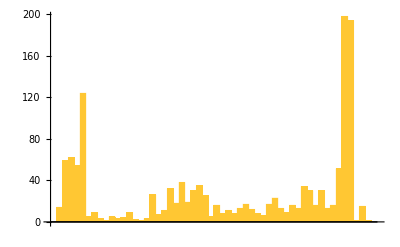

```mathematica
BarChart[Length/@ GroupBy[Values[$LifeData], #Year&]]
```

```mathematica
Divide[2, 4]
```

1/2

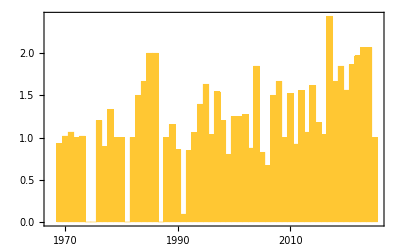

```mathematica
BarChart[Quiet[ReplaceAll[Divide@@
(Table[Lookup[#, i, 0], {i, 1969, 2025}]&/@{Total[#[[All, 2]]]&/@GroupBy[Normal[Count[#, None]&/@ xresall], $LifeData[#[[1]]]["Year"]&] ,Length/@ GroupBy[Values[$LifeData], #Year&]}), Indeterminate->0]], Frame->True, FrameTicks->{{True, Automatic}, {Table[If[Mod[i , 10] == 2, {i,i + 1968}, i], {i, 2, 2025 - 1969 + 1, 10}], True}}]
```

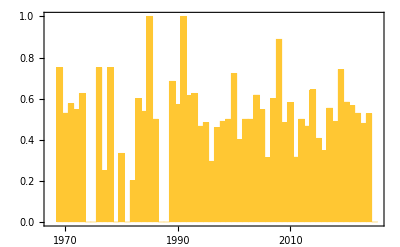

```mathematica
BarChart[Quiet[ReplaceAll[Divide@@
(Table[Lookup[#, i, 0], {i, 1969, 2025}]&/@{Total[#[[All, 2]]]&/@GroupBy[Normal[Count[#, None]&/@ resall], $LifeData[#[[1]]]["Year"]&] ,Total[#[[All, 2]]]&/@GroupBy[Normal[Length/@ resall], $LifeData[#[[1]]]["Year"]&]}), Indeterminate->0]], Frame->True, FrameTicks->{{True, Automatic}, {Table[If[Mod[i , 10] == 2, {i,i + 1968}, i], {i, 2, 2025 - 1969 + 1, 10}], True}}]
```

```mathematica
Table[Lookup[#, i, 0], {i, 1969, 2025}]&/@
```

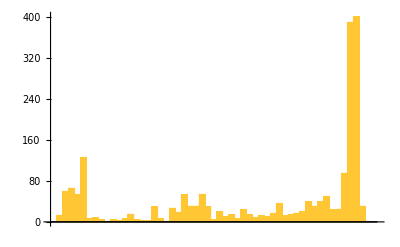

```mathematica
BarChart[Total[#[[All, 2]]]&/@GroupBy[Normal[Count[#, None]&/@ xresall], $LifeData[#[[1]]]["Year"]&]]
```

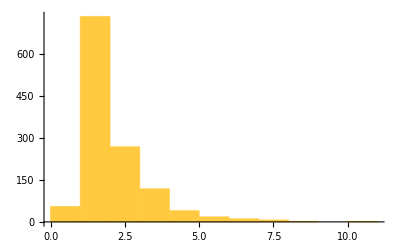

```mathematica
Histogram[Count[#, None]&/@ xresall]
```

```mathematica
Map[xresall, Count[#, None]&]
```

<|Beehive→{None},Blinker→{None},Block→{None},Crotchet→{None},Domino→{None},Dot→{None},Duoplet→{None},Glider→{None},Line of three→{Blinker},Loaf→{None},Pre-block→{None},R-pentomino→{None},Short table→{None},Traffic light→{None},Aircraft carrier→{None},Banana spark→{None},Barge→{None},Beacon→{None},B-heptomino→{None},Bi-block→{None},Bipole→{None},Blockade→{Block},Boat→{None},Bookend→{None},Bun→{None},Cavity→{None},Century→{None},C-heptomino→{None},Claw→{None},Clock→{None},Crinkly heptomino→{None},Cuphook→{None},Diagonal on-off→{None},E-heptomino→{None},F-heptomino→{None},Figure eight→{None},Gosper glider gun→{Block,None,None},Heavyweight spaceship→{None},Herschel→{None},Hertz oscillator→{None},Honey farm→{Beehive},House→{None},Leg→{None},Lightweight spaceship→{None},Line-of-six spark→{None},Long barge→{None},Long boat→{None},Long ship→{None},Long snake→{None},Middleweight spaceship→{None},Pentadecathlon→{None},Period-60 glider gun→{Block,None,Glider,None,None,None,None,None},Phi spark→{None},Pi-heptomino→{None},Pinwheel→{None},Pole 2→{},Pole 3→{None},Pole 4→{None},Pond→{None},Pulsar→{None},Quadpole→{None},Queen bee→{None},Queen bee shuttle→{Block,Queen bee},Ship→{None},Snake→{None},Table→{None},Tail→{Leg},Toad→{None},Tripole→{None},Tub→{None},Tumbler→{None},V spark→{None},Z-hexomino→{None},3c/10 pi wave→{None,None,None,None},Almosymmetric→{None},Big S→{None},Block-laying switch engine→{Block,None,None},Blonk-tie→{None},Boat-bit→{Snake,Glider,Glider,None},Candelabra→{None},Canoe→{None},Cap→{None},Cauldron→{None},Cis-boat with tail→{None},Double ewe→{None,None},Eater 1→{None},Ecologist→{None,None,Lightweight spaceship,Lightweight spaceship,None},Flutter→{},French kiss→{None},Gliders by the dozen→{None},Gray counter→{None},Hat→{None},Hook with tail→{None},Hustler→{None},Integral sign→{None},Interchange→{None},Iwona active region→{None},Kok's galaxy→{None},Light bulb→{None},Long canoe→{None},Long.b3 snake→{None},Mango→{None},Negentropy→{None},New gun 1→{None,Block,Glider,B-heptomino,None},Noah's ark→{Switch engine},Octagon 2→{None},Orthogonal on-off→{None},p60 glider shuttle→{Glider,Pentadecathlon},Phoenix 1→{None},Pi ship 1→{Block,None,None},Piston→{House,None},Pressure cooker→{None},Puffer 1→{None,None},Quad→{None},Quasar→{None},Scrubber→{None},Shillelagh→{None},Spark coil→{House},Spiral→{None},Squaredance→{None},Switch engine→{None},Thunderbird→{None},Titanic toroidal traveler→{None},Trans-boat with tail→{None},Tub with tail→{None},Twin bees shuttle→{Block,None},Twin bees shuttle spark→{None},Two eaters→{None},Two-glider octomino→{None},U-turner→{None},Very long boat→{None},Very long snake→{None},Washerwoman→{Tub,None},1-2-3→{None},Airforce→{None},Barge siamese loaf→{None},Beehive with tail→{None},Biting off more than they can chew→{None},Block on griddle→{None},Block on table→{None},Boat-tie→{None},Boat with long tail→{None},Boss→{None},Broken snake→{None},Burloaferimeter→{None},Carrier siamese carrier→{None},Cis-barge with tail→{None},Cis-shillelagh→{None},Cis-very long hook with tail→{None},Claw with tail→{None},Diamond ring→{None},Dinner table→{None},En retard→{None},Four skewed blocks→{Block},Frog II→{None},Germ→{None},Hooked integral→{None},Loading dock→{None},Long hook with tail→{None},Long integral→{None},Long shillelagh→{None},Long⁴ snake→{None},Loop→{None},Mathematician→{None},Melusine→{None},Multum in parvo→{None},Penny lane→{None},Prodigal→{None},Protein→{None},Pyrotechnecium→{None},RF28B→{R-pentomino,Tub,Eater 1},Roteightor→{Eater 1,None},Schick engine→{None,None},Snacker→{None},Snake dance→{None},Snake pit→{None},Snake siamese snake→{None},Sombreros→{None},Surprise→{None},Trans-barge with tail→{None},Trans-very long hook with tail→{None},Tub with long tail→{None},Tub with very long tail→{None},Two-glider mess→{None,None},Very long shillelagh→{None},Worker bee→{None},$rats→{None},Asymmetric amphisbaena→{None},aVerage→{None},Barge with very long tail→{None},Beehive at beehive→{None},Beehive at claw→{None},Beehive on table→{None},Beehive with hooked tail→{None},Beehive with nine→{None},Block on cap→{None},Block on cover→{None},Boat tie eater head→{None},Boat tie eater tail→{None},Boat tie long boat→{None},Boat tie long snake→{None},Broken elevener→{None},Bun with feather→{None},Canoe siamese snake→{None},Carrier bridge carrier→{None},Carrier bridge snake→{None},Carrier bridge table→{None},Carrier siamese canoe→{None},Carrier siamese hook-with-tail hook→{None},Carrier siamese hook-with-tail tail→{None},Carrier siamese shillelagh→{None},Carrier siamese tub with tail→{None},Carrier siamese very long snake→{None},Carrier tie ship→{None},Chemist→{None},Circle of fire→{None},Cis-barge with nine→{None},Cis-block on long bookend→{None},Cis-boat amphisbaena→{None},Cis-boat trans-line tub→{None},Cis-boat with long.b3 tail→{None},Cis-carrier down on table→{None},Cis-carrier-tie→{None},Cis-carrier tie snake→{None},Cis-carrier up on table→{None},Cis-fuse with two tails→{None},Cis-long barge with tail→{None},Cis-long⁴ hook with tail→{None},Cis-mango with tail→{None},Cis-ship on table→{None},Cis-snake-tie→{None},Cis-tub with long⁴ tail→{None},Cis-very long hook with nine→{None},Claw at claw→{None},Claw siamese tub with cape→{None},Claw with boat with tail→{None},Claw with nine→{None},Crowd→{None},Double claw→{None},Down snake on table→{None},Eater head siamese eater head→{None},Eater head siamese eater tail→{None},Eater head siamese long snake→{None},Eater plug→{None},Eater tail siamese eater tail→{None},Eater tail siamese long snake→{None},Eater with head feather→{None},Eater with tail feather→{None},Egyptian walk→{None},Fuse with tail and nine→{None},Fuse with tail and very long tail→{None},Fuse with two long tails→{None},Gull with tub→{None},Honeybarge→{None},Hook-with-tail hook siamese snake→{None},Hook-with-tail tail siamese snake→{None},Hook with tail with cape→{None},Hook with two tails→{None},Inflexion→{None},Integral with hook and tail→{None},Integral with tub and tail→{None},Long boat with long tail→{None},Long hook line tub→{None},Long.b3 integral→{None},Long integral with boat→{None},Long snake siamese long snake→{None},Long snake with feather→{None},Long tub-claw with tail→{None},Mazing→{None},Newshuttle→{None,Eater 1,None,None},p54 shuttle→{B-heptomino,Eater 1,None},Pedestle→{None},Pulsar quadrant→{None},Rotated table→{None},Shillelagh siamese snake→{None},Ship tie snake→{None},Siesta→{None},Snake bridge snake→{None},Snake siamese very long snake→{None},Snorkel loop→{None},Teardrop with cape→{None},Teardrop with claw→{None},Technician→{None},Trans-barge with nine→{None},Trans-block on long bookend→{None},Trans-boat amphisbaena→{None},Trans-boat trans-line tub→{None},Trans-boat with long.b3 tail→{None},Trans-carrier down on table→{None},Trans-carrier-tie→{None},Trans-carrier tie snake→{None},Trans-carrier up on table→{None},Trans-long barge with tail→{None},Trans-mango with tail→{None},Trans-ship on table→{None},Trans-snake-tie→{None},Trans-tub with long⁴ tail→{None},Trans-very long hook with nine→{None},Tub bend line tub→{None},Tub with tail siamese snake→{None},Tub with tail with cape→{None},Tub with two down cis tails→{None},Tub with two down trans tails→{None},Tub with two up cis tails→{None},Tub with two up trans tails→{None},Twelve loop→{None},Two pulsar quadrants→{None},Up snake on table→{None},Very long claw with tail→{None},Very long melusine→{None},Very long prodigal→{None},Buckingham's p13→{None,None},Extremely impressive→{None},Pentant→{None},Unix→{None},38P11.1→{None},44P7.2→{None},Blinkers bit pole→{None},Eater 3→{None},Four eaters hassling lumps of muck→{Eater 1,None},Fox→{None},Pentoad→{Z-hexomino,Eater 1},Tritoad→{None},Why not→{None},Gourmet→{None,None},Harbor→{None},Sixty-nine→{Mazing,None},Octagon 4→{None},Eureka→{Tub,None},Heavyweight emulator→{None},Lightweight emulator→{None},Middleweight emulator→{None},p29 pre-pulsar shuttle→{Block,None,Tub,Eater 1},Heart→{None},p47 pre-pulsar shuttle→{Blinker,Block,None,Tub,Eater 1},Trice tongs→{None},p10 traffic light hassler→{Block,None},p26 pre-pulsar shuttle→{Blinker,None,Beacon,None},Tumbling T-tetson→{Figure eight,None},Two pre-L hasslers→{None,None},6 bits→{Glider,None,None,Pentadecathlon},Blinker puffer 1→{Middleweight spaceship,None},Carnival shuttle→{None,None,None,Monogram,None},Hectic→{Block,Glider,Queen bee},Jack→{None},p36 toad hassler→{Toad,Snacker},Sailboat→{Kok's galaxy,None,None},Pulshuttle V→{None,None,None},Stillater→{None},p55 pre-pulsar hassler→{None,Eater 1,Eater 3,None},Achim's p4→{None},Jam→{None},Mold→{None},106P135→{Block,Glider,None,None,Pentadecathlon},119P4H1V0→{None,None},1-2-3-4→{None},25P3H1V0.1→{None},64P2H1V0→{None},84P3H1V0.1→{None},Baker's dozen→{Block,None,Caterer},Bent keys→{None},Big glider→{None},Caterer→{None},Cross→{None},Double caterer→{None},Fumarole→{None},Monogram→{None},Odd keys→{None,None},Short keys→{None},Skewed traffic light→{None},Statorless p6→{None},Tempest→{None},T-nosed p4→{None},Triple caterer→{None},Turning toads→{None},Turtle→{None},Twirling T-tetsons 2→{None,Toad,None},Windmill→{None,None},22P4.3→{None},Loaflipflop→{None,None,Loaf,Pentadecathlon},New five→{None},Two blockers hassling R-pentomino→{Block,None,None},44P5H2V0→{None},117P9H3V0→{None},20P4→{None},25P3H1V0.2→{None},60P3H1V0.3→{None},70P2H1V0.1→{None},70P5H2V0→{None},Blinker puffer 2→{Middleweight spaceship,None},Brain→{None},Dart→{None},Edge-repair spaceship 1→{None},Fly→{None},Hivenudger→{None},Hivenudger 2→{None,None,None},Laputa→{None},Middleweight volcano→{None},Non-monotonic spaceship 1→{None},p44 pi-heptomino hassler→{Block,House,Heavyweight emulator},p50 glider shuttle→{Glider,None},Pushalong 1→{None},Ring of fire→{None},Sidecar→{None},Sparky→{None},Toaster→{None},Wickstretcher 1→{None,None},x66→{None},2.3.3→{None},A for all→{None},Boatstretcher 1→{None},Bracket pulsar→{None},Bracket quasar→{None},Cross 2→{None,None},Electric fence→{None},Enterprise→{None},Glider pusher→{Glider,Pentadecathlon,Eater 1,None},Muttering moat 1→{None},Orion→{None},Slow puffer 2→{Middleweight spaceship,Middleweight spaceship,None,None},Spacefiller 1→{None},Star→{None},Wing (spaceship)→{None,None},101→{None},134P25→{None,Eater 1,Middleweight volcano},186P24→{None,Tub,None,Eater 1,None,Monogram},233P3H1V0→{None},Achim's other p16→{Toad,None},Achim's p11→{Blinker,Block,Long barge},Achim's p144→{Block,Beehive,None},Achim's p16→{None},Achim's p8→{None},Bottle→{None},Crown→{None,Jam,Caterer,Heavyweight emulator},Fore and back→{None},Fountain→{None,None},Four blinkers around four blocks→{None},Jason's p6→{None},Metamorphosis II→{Block,None,None,None,None},New gun 2→{Block,Beehive,None,None,None},p124 lumps of muck hassler→{None,Block,Tub,Eater 1,Clock,None,None,None},p42 glider shuttle→{Block,None,Glider,None,Unix,None,Eater 3},p48 toad hassler→{None,Ship,Beehive,None,Toad,Figure eight,None},p50 traffic jam→{None,Octagon 2,Traffic light,Fumarole,None},p58 toadsucker→{Block,None,Tub,None,Eater 1,Toad,None},Pseudo-barberpole→{None},Rumbling river 1→{None},Ship in a bottle→{Ship,None},Smiley→{None},T-nosed p6→{None},Traffic circle→{None,None,Mold,Mold,Traffic light,Traffic light},Trivial p6-1→{None},Twin bees shuttles hassling blinker→{None,Blinker,Block,B-heptomino,None},Vex→{Blinker,None},124P21→{None,Caterer,44P7.2},145P20→{None,Middleweight volcano,None},22P36→{None,Eater 1},Coe ship→{None},Four molds hassling eight blocks→{Bi-block,None,Mold,Mold},Heavyweight volcano→{None,None},Max→{None},p156 Hans Leo hassler→{None,None,Eater 1,Caterer,Heavyweight emulator,None},p18 bi-block hassler→{None,None,None,Unix},p35 beehive hassler→{None,Fumarole,Fumarole,None,None},p60 traffic light hassler→{None,Pentadecathlon,None},Period-256 glider gun→{Block,Snake,Glider,Herschel,Eater 1},Pi orbital→{Block,None,None,None,Caterer,Heavyweight emulator,None},R64→{Block,None,Herschel,None},Spacefiller 2→{None},Zweiback→{Loaf,None},46P4H1V0→{None},49P88→{None,Eater 1},60P5H2V0→{None},B-52 bomber→{Block,None,None,Glider,Tub,None,Mold},Conduit 1→{Block,Snake},F117→{Block,Snake,None,Herschel,Eater 1},Fx119→{Block,None,Herschel,Eater 1},Fx119 inserter→{Block,Herschel,Eater 1},Fx158→{None,Herschel,Eater 1,None},Fx77→{Block,None,Herschel,Eater 1,Pond},Glider stopper→{Block,Glider,Beehive,Eater 1},Glider to block→{Block,Glider,Boat,Eater 1},Herschel receiver→{Block,Snake,Glider,Glider,Boat,Beehive,None},L112→{Block,None,Aircraft carrier,Herschel,Eater 1},L156→{Block,Snake,Tub,None,Herschel,Eater 1},p52 R-pentomino hassler→{None,Tub,T-nosed p4,T-nosed p4,Eater 3},Period-184 glider gun→{Eater 1,None},Period-246 glider gun→{Block,None,Eater 1,None,Unix,p6 thumb},Period-690 glider gun→{Block,None,Eater 1,None,Queen bee,None},R190→{Block,Snake,None,Herschel,Eater 1,None,None},RR56H→{Block,R-pentomino,None},Snail→{None},Swan→{None,None},168P22.1→{None,None},258P3→{None},258P3 on Achim's p11→{Blinker,Block,Long barge,258P3},29P9→{None},44P14→{None},54P17.1→{None},Babbling brook 1→{None},Champagne glass→{None},Coe's p8→{Block,None},Elkies' p5→{None},F116→{Block,None,Herschel,Eater 1,None},F166→{Block,Snake,None,Eater 1,None},Fx153→{Block,Snake,None,Herschel,Eater 1},Fx176→{Block,None,Herschel,Eater 1,Tub with tail,None},Hebdarole→{None},Herschel transmitter→{Snake,Herschel,Eater 1,None},HF95P→{Block,Herschel,Eater 1},HFx58B→{Block,None,None,Herschel,None,Eater 1,None,None,Figure eight},Lx200→{Block,Snake,None,Eater 1,None},p15 pre-pulsar spaceship→{None,None,None},p6 pipsquirter→{None},Period-24 glider gun→{None,Glider,None,Eater 1,None,None,None},Period-44 glider gun→{Block,None,Eater 1,Heavyweight emulator},Period-44 MWSS gun→{Pre-block,Block,Eater 1,None,None,None,None,None},PF35W→{Pi-heptomino,Eater 1,None},RF48H→{R-pentomino,None,Loaf},Rx202→{Block,Snake,None,Herschel,Eater 1,None,None},Spider→{None},Vacuum (gun)→{Block,None,Eater 1,None,None,None},Waveguide 1→{None},28P7.1→{None},28P7.2→{None},37P10.1→{None},41P7.2→{None},Bx125→{Block,None,Herschel,Eater 1,None},Bx222→{Block,Snake,None,Herschel,Eater 1,None,None},Callahan G-to-H→{Block,Glider,None,Beehive,Eater 1,None},Diuresis→{None,None,None},p5 bouncer→{Glider,Glider,None,None,None},p6 bouncer→{Block,Glider,None,None},p8 bouncer→{Block,Glider,Glider,None,Figure eight},Pre-pulsar spaceship→{None,Spider},RNE-19T84→{R-pentomino,Beehive,Eater 1,None},Superfountain→{None,None},Thumb 1→{None},Wasp→{None},Canada goose→{None},Glider emulator→{Big glider,None},Orion 2→{None},p7 pipsquirter→{None},134P39.1→{None,None,None},295P5H1V1→{None},30P5H2V0→{None},72P6H2V0→{None},Crab→{None},Dragon→{None,None},Edge-repair spaceship 2→{None,None},Jason's p22→{None},Jason's p33→{Tub,Boat,None},p6 thumb→{None},Period-22 glider gun→{None,Glider,Eater 1,None,None},Silver's p5→{Snake,None},Weekender→{None},Wings→{None},55P9H3V0→{None},Backrake 1→{None},Boojum reflector→{Block,Glider,Tub,Eater 1,None},Coolout Conjecture→{None},Frothing puffer→{None},p130 shuttle→{Block,None,None,Loaf,None},Quad pseudo still life→{None},Triple pseudo still life→{None},123P27.1→{None},31P8H4V0→{None},50P35→{Blinker,Eater 1,None},69P48→{None},98P25→{Block,None,Fumarole},Blom→{None,None},Four eaters hassling four bookends→{Eater 1,None},Gabriel's p138→{None},Karel's p15→{None,Pentadecathlon},p15 bouncer→{Block,Glider,Glider,None,Pentadecathlon,None},p24 shuttle→{Block,None,None},(13,1)c/31 Pseudo-B climber→{Glider,Glider,None},Fire-spitting→{None},Jason's p11→{None},p4 pipsquirter→{None},p60 B-heptomino hassler→{None,None,B-heptomino,None,Unix},160P10H2V0→{None,None},35P4H1V1→{None},3-engine Cordership→{Block,Tub,None,None,None,None,None,None,None},B29→{None},Blonker→{None},Iwona→{Blinker,Pre-block,Iwona active region,None},Jason's p36→{None,Eater 1,Jam},Justyna→{Blinker,Pre-block,None},p6 shuttle→{Eater 1,None},Period-156 glider gun→{Block,None,None},23334M→{None},33P4H1V1→{None},37P7.1→{None},7468M→{None},86P5H1V1→{None},94P27.1→{Thumb 1,None},Crane→{None,None},Lidka→{Tub,None},One per generation→{None},p72 quasi-shuttle→{None,None,Figure eight},Seal→{None},Switch engine channel→{Boat,Switch engine},T-nosed p5→{None},274P6H1V0→{None,None},67P5H1V1→{None},Cyclic→{None},Demultiplexer→{Glider,Herschel,Eater 1},F171→{None,Herschel,Eater 1},Honeybit→{Block,Glider,Beehive,Pond,Lightweight spaceship},Ship+fishhook→{None},Sidewinder→{None,None,Lightweight spaceship},52P84→{None,None,None},78P70→{Block,Eater 1,None},Four eaters→{Eater 1},Karel's p177→{Crotchet,None},Karel's p28→{Block,None},Land of lakes→{None},p25 pre-pulsar shuttle→{Block,None,Eater 1,None,None},35201M→{None},Bulldozer→{None,None,None},Eve→{None,None},Scot's p5→{None},128P10.2→{Block,None},38P7.2→{None},44P12.3→{None},46P10→{Ship,Clock,None},48P22.1→{None},56P6H1V0→{None},68P32→{None},Beluchenko's p13→{Block,None},Beluchenko's p37→{Block,Loaf,None},Beluchenko's p40→{Block,None},Beluchenko's p51→{None,None},p11 pinwheel→{None,None},Period-88 glider gun→{Block,Glider,None,None,Figure eight,Figure eight},Rectifier→{Block,Glider,Beehive,Eater 1,None},110P62→{None,Block,None,None},24P10→{None},32829M→{Blinker,None},44P10→{None},56P27→{Block,Leg,None},58P5H1V1→{None,None},74P8H2V0→{None},Beluchenko's other p37→{Block,None,Eater 1,None},Ed→{None},Edna→{None},Ellison p4 HW emulator→{None,None,Snake,None},Fred→{None},Merzenich's p11→{Tub,None},Merzenich's p31→{Block,None},Merzenich's p64→{Block,None,None},p32 blinker hassler→{Block,Tub,None,None,None},p32 blinker hassler 2→{None,None,Tub,Ship,None,Figure eight,None,None},p44 traffic light hassler→{Ship,None,Mold,None,None},Period-45 glider gun→{Blinker,Block,Glider,Glider,None,None},5blink→{None},77P6H1V1→{None},G4 receiver→{Block,Glider,Tub,None,Eater 1},Glider to 2 blocks→{Block,Glider,Eater 1},Lobster→{None,None},Merzenich's p18→{None},Montana→{None},p11 double-length signal injector→{None},p48 pi-heptomino hassler→{Blinker,None,Eater 1,None},R126→{Ship,None,Beehive,Herschel,Eater 1},Swine→{None},37P4H1V0→{None,None},86P6H3V0→{None},HLx111R→{Block,Snake,None,Herschel,Eater 1,None},p26 dependent reflector loop→{Glider,Eater 1,None,None},p31 dependent reflector loop→{Block,Glider,Eater 1,None,None},Statorless p3→{None},135-degree MWSS-to-G→{Block,None,Middleweight spaceship},31.4→{None},31c/240 Herschel-pair climber→{Block,Herschel},AK-94→{Block,Eater 1,None,None},CC semi-Snark→{Block,Glider,Boat,Eater 1},Century eater→{None},Loafer→{None,None},Period-20 glider gun→{None,None,Fumarole,None,None,None},Pi splitter→{Block,Pi-heptomino,None},Snark→{Block,Glider,Eater 1,None},50P9→{None},65P48→{Block,None,None},90P51→{None,None},c/12 R-pentomino crawler→{Blinker,None,R-pentomino},Honey thieves→{None,None},Jaydot→{None},Pufferfish→{None},Pufferfish spaceship→{None,Pre-block,Block,Short table,None,None,None,None,None,None,None,None,None},34P5H2V0→{None},35P12.1→{None},45-degree MWSS-to-G→{Glider,Beehive,Eater 1,Lightweight spaceship,Middleweight spaceship,None,None},50P92.1→{Block,None,None},53P13→{None},B60→{Block,None,Herschel,None},Beehive stopper→{Block,Glider,Beehive,Eater 1,Ship+fishhook},BLx19R→{Block,B-heptomino,Ship+fishhook},BNE14T30→{Block,None,None},BRx46B→{Block,Beehive,None},CBx37C→{Eater 1,None,Block on table},HL75P→{Block,None,Herschel,Eater 1},H-to-MWSS→{Block,Boat,None,Beehive,Herschel,Eater 1,None,Middleweight spaceship},Ocellus→{Block,Tub,None,p6 thumb,p6 thumb},p18 honey farm hassler→{Eater 1,None},p29 traffic-farm hassler→{Tub,None,None},p58 pre-pulsar shuttle→{None,None},Sidesnagger→{Block,Boat,Loaf},Simkin glider gun→{Block,Eater 1,None,None},Simkin's p60→{Block,Century,None,None},SW1T43→{Block,Herschel,Tub with tail,None},Syringe→{Block,Glider,None,Eater 1,Beehive with tail,None},112P15→{None,None},132P7→{Line-of-six spark,Hat,None},600P6H1V0→{None,None,None,None},84P87→{Block,Tub,Eater 1,Loaf,None},Cloverleaf interchange→{None},Copperhead→{None},Cthulhu→{None},Fireship→{None,None},Grandfather problem→{None},p21 honey farm hassler→{Tub,None,None},p28 pre-pulsar shuttle→{Blinker,Block,None,Tub,Eater 1,Mold},p35 honey farm hassler→{Block,Boat,None,Eater 1},p4 bumper→{None,Glider,Glider,Eater 1,Loaf,None},p5 bumper→{Glider,Glider,Eater 1,Loaf,Middleweight volcano},p6 bumper→{Block,Eater 1,Loaf,None},p7 bumper→{Glider,Glider,Eater 1,Loaf,38P7.2},p8 bumper→{Block,Glider,Glider,Eater 1,Loaf,None},p9 bumper→{Glider,Glider,Eater 1,Loaf,Thumb 1},Professor→{None},Rattlesnake→{Snake,None},Rich's p16→{None,None},Scorbie Splitter→{Block,Glider,Eater 1,Beehive with tail,None},Spaghetti monster→{None,None,None},Statorless p5→{None},24827M→{None},28P7.3→{None},2-engine Cordership→{Block,None,None,None,None,None,None,None},339P7H1V0→{None,Blinker,None,None,None,None,None,None,None},CC semi-cenark→{Block,Glider,Boat,Eater 1,None,None},CP semi-cenark→{Block,Glider,Boat,Eater 1,None,None},CP semi-Snark→{Block,None,Eater 1,None,31.4},F131→{Block,Boat,None,Herschel,Eater 1,None},p46 gliderless MWSS gun→{Block,Eater 1,None,None,None},Period-92 glider gun→{Block,Glider,Eater 1,None,None,None,None},Quadri-Snark→{Block,None,Eater 1,None,None},Runny nose→{None},Tanner's p46→{Block,Snake,None,Eater 1,None},Tremi-Snark→{Beehive,Eater 1,None},209P8→{Figure eight,None},33P3.1→{None},34P14 shuttle→{Block,None},42100M→{None},54P3H1V0→{None},55P10→{None},68P16→{Pre-block,Block,None},68P9→{None},Bronco→{Block,Glider,None,Eater 1,None,Eater 3},Cottonmouth→{None,None,None},Homer→{None},Jormungant's G-to-H→{Block,Glider,Glider,None,None,None},MWSS behind Coe ship→{Lightweight spaceship,None},p36 shuttle→{Block,None,None},p3 bumper→{Glider,Glider,Eater 1,Loaf,None},p46 gliderless LWSS gun→{Block,Pi-heptomino,Eater 1,Lightweight spaceship,Canoe,None,None,None},p4 bouncer→{Block,Glider,Glider,None,None},p5 pipsquirter→{Block,None},p64 thunderbird hassler→{Blinker,None,Figure eight},p9 bouncer→{Block,Glider,Glider,Eater 1,None,None},Period-33 glider gun→{Block,Glider,None,None,None,None,None,None,None,None},Sir Robin→{None},Wilma→{None,None},180P8→{None},47575M→{None},64P6→{None},66P13→{None,None},74P85→{None,None},David Hilbert→{None,None,None,None,None,None},Dueling banjos→{B-heptomino,Eater 1,Block on table,None},R49→{Block,Snake,None,None,None},Scholar→{None,None},104P9→{50P9,None},186P7H2V0→{None,None,None,None,None},409P6H1V0→{None,None,None,None,None},49768M→{None},Anura→{None},Bandersnatch→{Block,Glider,Eater 1,Loaf,None},Beehive push catalyst→{Beehive,None},Doo-dah→{None,None,Weekender},L122→{Block,None,Beehive,Herschel,Eater 1,None,None},p143 Bandersnatch loop→{Block,Glider,Eater 1,Loaf,None},Rob's p16→{None},Soba→{None,None},Unnamed tagalong 23P4H2V0→{None},50093M→{None},52513M→{None},62P7→{None},66P62→{Block,None,None},72P21→{Ship+fishhook,None},754P7→{None},Gallus→{Block,Glider,Tub,None},Nihonium→{Block,Snake,None,None},p11 bouncer→{Block,Glider,Glider,None,p11 domino sparker},p11 domino sparker→{None},p128 wing shuttle→{None,None,None,None},p196 pi-heptomino hassler→{Block,Pi-heptomino,None},p21 B-heptomino hassler→{Block,Boat,None,None},p32 honey farm hassler→{Block,Eater 1,None,Mold,Figure eight},p3 pipsquirter→{None,None},p486 R-pentomino hassler→{Block,None,p6 thumb,p6 thumb},p4 syringe→{Block,Glider,None,Eater 1,Block on table,None},p576 R-pentomino hassler→{None,Block,None,None,None},p76 pi-heptomino hassler→{Pi-heptomino,Eater 1,None,Heavyweight emulator},p96 honey farm hassler→{None,None,Figure eight},Period-117 glider gun→{Block,None,50P9},Period-144 glider gun→{Block,Glider,None,None,None,None},Period-54 glider gun→{Block,Glider,Eater 1,None,None,None},Period-55 glider gun→{Glider,Eater 1,None,None,None},Raucci's p74→{None,Eater 1},T-nosed p7→{None,None},Traffic stop→{Eater 1,None},112P57→{None,Eater 1,None,None,None},120P34→{Pi-heptomino,Eater 1,None,Eater 3},20-cell quadratic growth→{Blinker,Pre-block,None,None},232P7H3V0→{None,None,None},255P132→{None,None,None,None,None,None,None,None,None,None},30P25→{None},30P3→{None},32P21→{Block,Tub,None},32P4H2V0→{None},34P20→{Block,None},34P7→{None,None},35P12H6V0→{None,None,Heavyweight spaceship},36P25→{Block,Eater 1,None,None},42P14→{None,None,Ship+fishhook},43P54→{Block,Toad,Snake,None,Eater 1},52P44→{Block,Eater 1,Toad,None},54P94→{Pre-block,Block,Eater 1,None},55P23→{Block,None,Eater 1,None},58P37→{Eater 1,None},58P8H4V0→{None,None},62P83→{Block,None,Eater 1},66P106→{Blinker,None,Eater 1,Toad,Clock,None},70P23→{Block,Pi-heptomino,Eater 1},70P26→{Block,None,None},74P127→{Block,Tub,Eater 1,None},74P34→{House,Eater 1},76P86→{Block,None,Eater 1},84P199→{Block,None},92P23→{Tub,Eater 1,None,None},92P59→{Blinker,Eater 1,None},Charity's p16→{Block,None,Figure eight},Chucklebait→{None},CL48C→{Eater 1,None,None},Diamondback→{Eater 1,None},Grid's p16→{Block,Toad,None},HRx65R→{None,Herschel,Eater 1,None},HRx74B→{Block,Herschel,None},Meatball→{None},NW-2T16→{Block,None,None},P10 domino fountain→{None,None,None},p111 R-pentomino hassler→{Block,R-pentomino,Eater 1,None,None},p112 puffer→{Lightweight spaceship,None,Middleweight spaceship},p11 thumb→{None},p129 R-pentomino hassler→{R-pentomino,Eater 1},p146 pi-heptomino hassler→{Block,Toad,Boat,Eater 1,None},P16-assisted period-32 glider gun→{None,Block,None,None,None,None},p23 honey farm hassler→{Eater 1,None,None},p28 block puffer→{Lightweight spaceship,None},p39 pi-heptomino hassler→{Block,Snake,Boat,Pi-heptomino,None,None},p43 pi-heptomino hassler→{Blinker,Block,Pi-heptomino,Eater 1},p45 pi-heptomino hassler→{Block,Boat,None,Pentadecathlon},p49 R-pentomino hassler→{None,None},p4-assisted period-28 glider gun→{None,Block,Glider,None,Eater 1,None,None},p58 pi-heptomino hassler→{Block,House,Eater 1},p59 dependent reflector loop→{Block,Eater 1,None,None},P6 domino fountain→{None,House,None},p6 honey farm hassler→{Toad,None,None,None},p71 honey farm hassler→{Eater 1,None,None},p73 lumps of muck hassler→{Tub,Eater 1,None,None},p75 I-heptomino hassler→{None,None,Middleweight volcano},p79 pi-heptomino hassler→{Snake,House,Eater 1,None},p82 pi-heptomino hassler→{Block,Eater 1,Clock,None,None},p84 honey farm hassler→{Eater 1,None},p85 R-pentomino hassler→{Block,R-pentomino,Eater 1,Fumarole},p86 R-pentomino hassler→{Block,Eater 1,None},p8 glider reflector→{Block,Glider,Eater 1,None,None},p94 R-pentomino hassler→{Block,Eater 1,None},Period-113 glider gun→{Block,Eater 1,None},Period-25 glider gun→{None,Fumarole,None},Period-27 glider gun→{Block,Leg,None,None,Eater 1,None},Period-34 glider gun→{Glider,None,Eater 1,Long hook with tail,None,None,None,None,Chucklebait,None,None},Period-43 glider gun→{Tub,None,None},Period-48 glider gun→{Glider,None,None,Eater 1,None,None,None},Period-51 glider gun→{Glider,Tub,Eater 1,None,None},Raucci's p102→{None,Eater 1,None,None,Unix},Raucci's p38→{None,Eater 1,None},Speed tunnel→{None,Block,Glider,None,Beehive,None,None,None,None},Taco→{None,None},Twin bees shuttle on 21P4.1→{Block,None,None},Unique father problem→{None},Unsynthesizable oscillator 1→{None},0-degree colour-preserving reflector (March 2023)→{Bi-block,Glider,Eater 1,None,None,None},112P23→{Pi-heptomino,Eater 1,None,None},116P101→{Block,Eater 1,None,None},32P21 phase-shifting p5→{Block,Tub,None,None},42P38→{Blinker,R-pentomino,Eater 1,Toad},44P49→{Block,Eater 1,None},51P384→{Blinker,Block,None,None},72P119→{Block,Eater 1,None},86P107→{Block,Eater 1,None},94P53→{None,Ship+fishhook,None},Charity's p25→{Blinker,None,None},Charity's p30→{Block,None},Cribbage→{None,Eater 1,None},G-to-pi catalyst (August 2023)→{Block,Glider,None},Mold on fire-spitting→{None},Odd traffic stop→{Eater 1,None},p126 R-pentomino hassler→{Eater 1,Clock,None,None},p13 domino sparker→{B-heptomino,None},p140 two-glider octomino hassler→{Block,Tub,Eater 1,None},p16 century shuttle→{Toad,Tub,None},p17 R-pentomino hassler→{Hook with tail,None,None},p224 lumps of muck hassler→{None,None,None,Figure eight,Figure eight},p24 gliderless LWSS gun→{Lightweight spaceship,None,Kok's galaxy,None,None},p26 honey farm hassler→{Block,None,Eater 1,Clock},p280 U-turner hassler→{None,Tub,U-turner,Figure eight,Figure eight,Figure eight,Figure eight},p41 pi-heptomino hassler→{Boat,None,Eater 1,None,None},p47 lumps of muck hassler→{None,None,None},p49 pi-heptomino hassler→{Block,None,Loaf,None,Ship+fishhook},p59 pi-heptomino hassler→{Snake,House,None},p67 B-heptomino hassler→{Block,None,None},p68 century hassler→{Eater 1,None,Block on table},p76 pi-heptomino shuttle→{Beehive,None,Eater 1},p82 lumps of muck hassler→{Block,None,None},p93 R-pentomino hassler→{Block,Eater 1,None,None},Period-201 glider gun→{Block,Eater 1,None},Period-49 glider gun (April 2023)→{Block,Glider,Eater 1,None,None,None,None,None,None},Period-61 glider gun (2023)→{None,None,Block,Glider,Eater 1,None,None,None,None,None},Snark64→{Block,Beehive,Eater 1,None,None,Chucklebait},Walrus→{None,None},tnosep8sparker→{None},50p8sparker→{None},36p8sparker→{None},p10lonedotsparker→{None,None},p7honeyfarmhassler→{None},p8honeyfarmhassler→{Eater 1,None},p9honeyfarmhassler→{None,Eater 1,None},p9honeyfarmhassler2→{None,None},p9honeyfarmhassler3→{50P9,None},p10honeyfarmhassler→{None,None,Fumarole,None,None},p11honeyfarmhasslers→{Snake,Eater 1,None,None,None},p12honeyfarmhassler→{None,None,None,Heavyweight emulator,None,T-nosed p4},p12honeyfarmsparker→{House,None,None},p12honeyfarmhassler2→{Block,Eater 1,None,Unix},p12honeyfarmhassler3→{Eater 1,None},p22honeyfarmhassler→{None,Eater 1},p27bananasparker→{Eater 1,None,None},p27honeyfarmhassler→{Eater 1,None,None,None},p27d2honeyfarmhassler→{Block,Eater 1,None,None},p33honeyfarmhassler2→{Block,Eater 1,None},p34honeyfarmhassler→{Long hook with tail,None,None,None},p34mod17honeyfarmhassler→{Tub,None},p39honeyfarmhassler→{Block,Eater 1,None,None,None},p43honeyfarmhassler→{Eater 1,None},p44honeyfarmhassler2→{None,None,None},p46honeyfarmhassler2→{Block,None,None,None},p46longbunhassler→{Block,Beehive,Eater 1,None,None},p47honeyfarmhassler→{None,None},p49honeyfarmhassler→{None,None},84p51→{Tub,Eater 1,None,None},p51honeyfarmhassler→{Block,Tub,Boat,None},p52honeyfarmhassler2→{None,Mold,None,None},p52honeyfarmhassler3→{Block,Eater 1,Tub with tail,None,Chucklebait},p52honeyfarmhassler4→{Block,Eater 1,Toad,None,None,None,None},p54honeyfarmandbhassler→{Block,Eater 1,None,None,None},p56honeyfarmhassler→{Figure eight,Kok's galaxy,None},p56c2honeyfarmhassler→{Kok's galaxy,Figure eight,Kok's galaxy,None},p58honeyfarmhassler→{Block,Toad,Tub with tail,None},p62honeyfarmhassler→{Block,Bun,None,None},p64honeyfarmhassler→{Block,None,None},p64honeyfarmhassler2→{None,Figure eight,None},p65honeyfarmhassler→{Block,Tub,None,None},p65honeyfarmhassler2→{Block,Eater 1,None,None,None},p66honeyfarmhassler→{Blinker,None,House,Unix,None},p69honeyfarmhassler→{Eater 1,None,None},p70vsparker→{Snake,Eater 1,Loaf,None,Middleweight volcano},p70honeyfarmhassler→{Block,Eater 1,None,None},p72honeyfarmhassler→{Eater 1,None,64P6},p72honeyfarmhassler2→{None,Figure eight,64P6},p73honeyfarmhassler→{Block,Eater 1,None,None},cappedp74gun→{Block,None,Eater 1,None,None,None},p75honeyfarmhassler→{Block,None,None},p77honeyfarmhassler→{None,None},p77honeyfarmhassler2→{Eater 1,None,None,None},p80honeyfarmhassler→{Block,Boat,Eater 1,Chucklebait,None},p80honeyfarmhassler2→{Block,Tub,None,Ship+fishhook,None},p90honeyfarmhassler→{None,None,None,None,None,None},p90honeyfarmhassler2→{Block,None,None,None,None,Pentadecathlon},p91honeyfarmhassler→{Eater 1,None},cappedp91gun→{Block,Eater 1,None,None},p96honeyfarmhassler2→{Figure eight,None,Figure eight,Kok's galaxy},p96honeyfarmhassler3→{Block,None,None,Figure eight,Kok's galaxy},p97honeyfarmhassler→{Blinker,Block,Bun,Eater 1,None,None},p100honeyfarmhassler2→{None,Tub,None,None,Fumarole},p102honeyfarmhassler→{Block,Eater 1,None},p108honeyfarmhassler→{Block,Eater 1,None,None,None},p110honeyfarmhassler→{None,Middleweight volcano,Middleweight volcano,Middleweight volcano},p110honeyfarmhassler2→{Boat,None,55P10,55P10},p110honeyfarmhassler3→{None,V spark,Clock,Fox,None,None},p120honeyfarmhassler→{Eater 1,Caterer,None,Unix},p120honeyfarmhassler2→{None,Pentadecathlon,None,None},p128honeyfarmhassler→{None,None,None},p130honeyfarmhassler→{Eater 1,None,Middleweight volcano},p143honeyfarmhassler→{Block,Boat,Eater 1,None,Chucklebait},p147honeyfarmhassler→{Block,Boat,None,None},p182honeyfarmhassler→{Block,Eater 1,None,None},p30honeyfarmshuttle→{Block,Eater 1,None,None},p32doubleshuttle→{None,None,None},p36honeyfarmhassler→{Tub,Bun,Eater 1,None},p36honeyfarmhassler2→{None,None,None,Unix,Unix,None,None},p36honeyfarmhassler6→{Blinker,Eater 1,Jam,None,None,None,None,None,None},p36honeyfarmshuttlejp21→{Eater 1,None,None},p38honeyfarmshuttle→{Tub,Eater 1,None,None},p38honeyfarmshuttle2→{Block,None,Ship,Eater 1,None,None,None,None,None},p40honeyfarmhassler4→{Block,Eater 1,None,Mold,None,Kok's galaxy,None,None},p40honeyfarmhassler→{Block,None,Figure eight,None,Figure eight,Kok's galaxy,Kok's galaxy},p40andp50dominofountains→{None,None,None,Eater 1,None,None},p40honeyfarmshuttle→{Eater 1,Clock,None},p44honeyfarmhassler→{None,Block,Eater 1,None,None,None,None,None},p48honeyfarmhassler→{None,None,Star,None,None},p52honeyfarmhassler→{None,None,None,None,None,None},p60honeyfarmshuttle→{Eater 1,None,None},p60honeyfarmshuttle2→{Unix,Chucklebait,None},p136honeyfarmshuttle→{None,None,None,None},p220honeyfarmshuttle→{Snake,Boat,Eater 1,Loaf,None},p8rpentominohassler→{Eater 1,None},p12rpentominohasslers→{R-pentomino,None,p6 thumb,p6 thumb,p6 thumb,64P6},p13rpentominohassler→{Block,Eater 1,None,None},p23rpentominohassler→{Eater 1,None,None},p24rpentominohassler→{Block,None,None},p24rpentominohassler2→{Blonker,None},p30rpentominohassler→{None,None,None},p30rpentominohassler2→{None,Eater 1,None,None},p31rpentominohassler→{Block,R-pentomino,None},p32rpentominohassler→{R-pentomino,None,None,None},p32rpentominohassler2→{None,None,None,None},p35rpentominohassler→{None,None,None},p35rpentominohassler2→{Block,None,None,None,None},p35rpentominohassler3→{Block,Eater 1,None,None,None},p38rpentominohassler→{Blinker,Block,None,Eater 1,None,None,None},p45rpentominohassler→{Block,Boat,Eater 1,None,None,None},p49singlerpentominohassler→{None,None,None,None,None,None},p50rpentominohassler→{R-pentomino,None,None},p54rpentominohassler→{None,None,64P6},p57rpentominohassler→{Block,R-pentomino,None},p60rpentominohassler→{Block,Glider,Pentadecathlon,Tub with tail,None},p60rpentominohassler2→{None,R-pentomino,None,None},p64rpentominohassler2→{R-pentomino,None,Eater 1,None,None,Mold,Figure eight},p76rpentominoshuttle→{None,None,Hook with tail,None,None,None,None,None},p78rpentominohassler→{Block,R-pentomino,Tub,Eater 1,None},p86rpentominohassler2→{Eater 1,None,None},p88rpentominoshuttle→{Eater 1,Figure eight,Figure eight,tnosep8sparker,None},p88rpentominohassler→{Block,None,None,Kok's galaxy},p90rpentominohassler→{R-pentomino,None},p96rpentominohassler→{Eater 1,None},p102rpentominohassler→{None,House,None,None},p104rpentominohassler→{Block,None,Ship+fishhook,Figure eight},p105rpentominohassler→{R-pentomino,Pentadecathlon,Pentadecathlon},p109rpentominohassler→{R-pentomino,Beehive,Eater 1,None},p112rpentominohassler→{Block,Boat,None,None},p120rpentominohassler→{R-pentomino,Figure eight,Pentadecathlon,Figure eight,Figure eight,Figure eight},p122rpentominohassler→{None,Block,V spark,Tub,Eater 1,None,Tub with tail},p127rpentominohassler→{Tub,Eater 1,None,None,None},p135rpentominohassler→{Block,Eater 1,None,None,None},p140rpentominohassler→{Block,Eater 1,None,62P7,None},p140rpentominoshuttle→{None,Fumarole,None},cappedp140gun→{Block,None,Eater 1,None,None,None,None,62P7},p146rpentominohassler→{Block,Tub,Eater 1,None},p147rpentominohassler→{Block,R-pentomino,Eater 1,None,None},p150rpentominohasslerglidergun→{Blinker,None,None,Eater 1,None,None,None},p150rpentominohassler→{Block,Snake,R-pentomino,Toad},p156rpentominohassler→{R-pentomino,Boat,44P12.3,44P12.3,44P12.3,44P12.3},p166rpentominohassler→{Block,R-pentomino,None,None,None},p175rpentominohassler→{Block,Eater 1,None,None,None},98p201→{Block,Eater 1,None},p253rpentominohassler→{Block,Beehive,None,Eater 1,None,None},p13piheptominowick→{Eater 1,None,None,None},p13piheptominohassler→{None,Eater 1,None,None,None},p14piheptominohassler→{None,Toad,Tub,None,None,Ship+fishhook,None},p15piheptominohassler2→{Eater 1,None,None,None},p18piheptominohassler→{House,None},p20piheptominohassler→{Pi-heptomino,Middleweight volcano,Middleweight volcano},p25piheptominohassler→{Blinker,Block,Tub,Eater 1,None,None},p33piheptominohassler→{Pi-heptomino,None,None},p36piheptominohassler→{V spark,Pi-heptomino,Eater 1,None,None},p36piheptominohassler2→{Block,Pi-heptomino,Eater 1,Mold,None},p39piheptominohassler2→{Block,House,Eater 1,None,None,None,None},p39c4piheptominohassler→{None,Block,House,Eater 1,None,None,None},p46piheptominohassler→{None,Block,Tub,B-heptomino,Eater 1,None},p46piheptominohassler2→{Pi-heptomino,Eater 1,None,None,None},p47piheptominohassler→{House,Eater 1,Claw with tail,None},p52piheptominohassler→{Block,V spark,Tub,House,Eater 1,None,Heavyweight emulator,None},p53piheptominohassler→{Block,Pi-heptomino,Eater 1,None,Ship+fishhook},p53piheptominohassler2→{V spark,None,House,Eater 1,None},p55piheptominohassler2→{Block,Crotchet,Pi-heptomino,Eater 1,None},p60piheptominohassler→{House,Eater 1,None,Ship+fishhook,Unix},p60piheptominohassler2→{None,None,House,None,None,None,Ship+fishhook},p61piheptominohassler→{Block,Eater 1,None,None,None},p65piheptominohassler→{Block,House,Eater 1,None,None,None},p68piheptominohassler→{Pi-heptomino,Eater 1,None,None},p68piheptominohassler2→{Block,House,Eater 1,None,None,None},p69piheptominohassler→{Pi-heptomino,Eater 1,None,None},p70piheptominohassler→{House,None},p70piheptominohassler3→{Crotchet,House,None,5blink},p72lumpsofmuckhassler→{Block,None,None,Figure eight,Unix},p72piheptominohassler2→{Block,Pi-heptomino,Eater 1,None},p76piheptominohassler4→{Block,Eater 1,Clock,None,None},p77pihassler→{Block,Snake,Tub,Pi-heptomino,Eater 1,Ship+fishhook},p78piheptominohassler→{Block,House,None,Unix},p78piheptominohassler2→{Blinker,Block,House,Eater 1,None,None},p79piheptominohassler2→{House,Eater 1,Loaf,None,None},p79picenturyhassler→{Ship,House,None,None,Eater 3,None},p80pihassler→{Block,House,None},p88piblonktiehassler→{House,Eater 1,Clock,None},p90piheptominohassler→{None,Block,House,Pentadecathlon,Eater 1},p92piheptominohassler→{Pi-heptomino,Eater 1,None,None,None},p95piheptominohassler→{Blinker,Block,None,House,Eater 1,Middleweight volcano,None},p100piheptominohassler→{Blinker,Block,Boat,Pi-heptomino,Eater 1},p108piheptominohassler→{Pi-heptomino,Eater 1,None,Caterer,None,Unix,None,Unix,None},p112piheptominohassler2→{House,Eater 1,None,None},p117piheptominohassler→{Block,Tub,House,Eater 1,None,None},p121piheptominohassler→{None,Block,Tub,None,None,None},p125piheptominohassler2→{None,House,None,Middleweight volcano},p126piheptominohassler3→{Toad,Snake,Eater 1,None,None},p64andp128piheptominohasslers→{None,Blinker,Block,Pi-heptomino,Eater 1,None,None},p128piheptominohassler2→{Blinker,Block,Toad,None,None},p129piheptominohassler→{Block,Short table,House,Eater 1,Loaf,Ship+fishhook},p129piheptominohassler2→{Pi-heptomino,None},p132piheptominohassler2→{None,Glider,House,Eater 1,Clock,None,Mazing},p158piheptominohassler→{Block,Pi-heptomino,Eater 1,None,None},p159piheptominohassler→{Blinker,Block,Pi-heptomino,None,None},p160piheptominoshuttle→{None,None},p182pihassler→{Block,Pi-heptomino,Eater 1,Long hook with tail,None},p186pihassler→{Block,Ship,Beehive,House,Eater 1,Unix,Unix},p9lumpsofmuckhassler→{None,None},p12lumpsofmuckhassler→{Block,None},p13lumpsofmuckhassler→{None,None,None},p21lomhassler2→{Block,None,62P7},p22lumpsofmuckshuttle→{None,None},p25lumpsofmuckhassler→{None,None,Middleweight volcano},p25singlelumpsofmuckhassler→{V spark,None,None,Ship+fishhook,None,None},p27lumpsofmuckhassler→{None,None,None},p34lumpsofmuckhassler→{None,Eater 1,None,Long hook with tail,None,None,Chucklebait},p35lumpsofmucksparker→{None,Middleweight volcano,None},p35lumpsofmuckhassler→{None,None},p36lumpsofmuckhassler→{None,None},p37lumpsofmuckhassler→{Loaf,None,None},p40lumpsofmuckhassler→{None,55P10},p40lumpsofmuckhassler2→{None,None,None,None,None},p42lumpsofmuckhassler→{None,Unix,None},p42lumpsofmuckshuttle→{Block,None,None,None,Unix,62P7},p42lumpsofmuckhassler2→{Clock,None,None},p46lumpsofmuckhassler→{Block,Eater 1,None,None},p46lumpsofmuckhassler2→{Block,Bi-block,None,None},p46lumpsofmuckhassler3→{Block,Glider,Eater 1,Clock,None,Tub with tail,Cis-boat with tail},p47lumpsofmuckhassler2→{Snake,Tub,None,None},p49lumpsofmuckhassler→{Beehive,Eater 1,None,None,None,None},p49lumpsofmuckhassler2→{Block,Boat,Eater 1,None,Tub with tail,None},p51lumpsofmuckhassler→{Block,Eater 1,None,None},p52lumpsofmuckhassler→{None,Block,Toad,None,Eater 1,None,None,None},p62lumpsofmuckhassler→{Leg,Eater 1,None,None,None},p66lumpsofmuckhassler→{None,Eater 1,None,None},p68lumpsofmuckhassler→{Block,None,Tub,Loaf,None,Mazing},p68lumpsofmuckhassler2→{Block,None,Snake,Boat,Eater 1,None,None},p70lumpsofmuckhassler→{Hook with tail,None,Tumbler,None,None},p75lumpsofmuckhassler→{None,None,None,None,None,None},p76lumpsofmuckhassler→{Eater 1,None,None},p80singlelumpsofmuckhassler→{None,None,None,None,None},p80lumpsofmuckhassler→{Tub,None,Fumarole,None},p80lumpsofmuckhassler2→{Eater 1,None,None,None},p84lumpsofmuckhassler→{Block,House,None,None,None},p88lumpsofmuckhassler→{None,Figure eight,None,Kok's galaxy},p88lumpsofmuckhassler2→{Block,Boat,Beehive,Eater 1,None,None,Figure eight,None},p96lumpsofmuckhassler→{None,Toad,None,None,None},p96lumpsofmuckhassler2→{None,Kok's galaxy,None},p98lumpsofmuckhassler→{Blinker,Block,Eater 1,None},p100lumpsofmuckhassler→{Block,Eater 1,Clock,None,None},p100lumpsofmuckhassler2→{Eater 1,Toad,None,None},p104lumpsofmuckshuttle→{None,Block,None,Figure eight,Figure eight,Kok's galaxy,Kok's galaxy,None},p105lumpsofmuckhassler→{Block,None,Fumarole,Middleweight volcano},p105lumpsofmuckhassler2→{Blinker,None,None,None,None},p108lumpsofmuckhassler→{Glider,Boat,Eater 1,Clock,None,Fox,None},p110lumpsofmuckhassler→{Eater 1,None,None,None},p110lumpsofmuckhassler2→{Block,Eater 1,None,Chucklebait},p115lumpsofmuckhassler→{Block,Eater 1,None,None},p138lumpsofmuckhassler→{Block,Snake,Eater 1,None,None,None},p140lumpsofmuckhassler→{None,None},p184lumpsofmuckhassler→{None,None},p14centuryhassler→{Eater 1,None,None},p16centuryhassler→{None,Block,Eater 1,None,None,Figure eight,None},p28centuryhassler→{None,None,None},p28centuryshuttle→{Block,None,None,None},p45picenturyhassler→{None,Block,Boat,None,Pentadecathlon,Eater 1,None},p54picenturyhassler→{Eater 1,Clock,None,None},p72centurylomhassler→{Eater 1,None,Heavyweight emulator,Figure eight},p72centuryhassler→{Block,None,None},p110centuryshuttle→{Eater 1,None,None,None},p139centuryhassler→{Eater 1,None,None},p174centuryshuttle→{V spark,Bookend,p6 pipsquirter,64P6,p6 pipsquirter,64P6},cl48cloop→{Bookend,None,None},p48bheptominohassler→{Block,None,Eater 1,None,None},p68bheptominohassler→{Block,None,None,Eater 1,None,None},p80twinbeesshuttle→{Block,Snake,None,None,Loaf},p36winghassler→{Hook with tail,None,None},p48rpentominohassler2→{Eater 1,None,None},p48longbunhassler→{Eater 1,Clock,None,None,None},p80procrastinatorhassler→{None,R-pentomino,Eater 1,None,Figure eight,Kok's galaxy,Figure eight,None},p12blonktiehassler→{None,64P6,64P6},p16uturnerhassler→{Block,Eater 1,U-turner,None,Kok's galaxy},p60uturnerhassler→{None,Pentadecathlon,Pentadecathlon,None,None,Fumarole,Ship+fishhook,None},p144uturnerhassler→{None,Block,V spark,Tub,None,U-turner,None,None,None,Figure eight,None,None,Figure eight},prepulsarshuttle22→{None,None},p26prepulsarhassler2→{Block,None,None,None},prepulsarshuttle32→{None,None},prepulsarshuttle35→{None,None,None},prepulsarshuttle36→{None,None,T-nosed p4,None},prepulsarshuttle36reduced→{Tub,None,Eater 1,None},prepulsarshuttle40→{None,None,Figure eight,Figure eight},prepulsarshuttle42→{Block,None,None},p48prepulsarshuttle→{None,Eater 1,Figure eight},p55prepulsarshuttle→{None,None,None},prepulsarshuttle60→{None,Caterer},prepulsarshuttle64→{Block,None,None,None},prepulsarshuttle65→{None,None,None},prepulsarshuttle88→{None,None,None},prepulsarshuttle90→{None,None,Caterer,Fumarole},p34dependentreflectorloop→{None,Glider,None,None,Eater 1,None},p53dependentreflectorloop→{Block,Glider,Eater 1,Block on table,None,None},135-degree LWSS-to-G→{Glider,Lightweight spaceship,None},139P7H1V0→{None,None},409P7→{None,None},86P118→{Block,Tub,Beehive,Clock,None,None},Goban→{Eater 1,None,None,None},L141→{Block,Tub,Boat,Herschel,Eater 1},Lx65 duplicator→{Block,None,Herschel,Eater 1,Loaf},P56 phi sparker→{Block,None,Eater 1,None,None,Ship+fishhook,None,None},Period-15 glider gun→{Eater 1,None,5blink,None},Period-36 glider gun→{None,Clock,Jam,Caterer,None,None,None},Period-53 glider gun→{None,Glider,Eater 1,None,None,None,None,None,None},Spartan G-to-W-to-H→{Block,Eater 1,None,None},Tarantula→{None}|>[Count[#1,None]]&

```mathematica
AssociationMap[Keys[xresall], Count[#, None]&]
```